# Tests on Graph Codes

## Nonisomorphic graphs for n=2 to n=9, and Eulerian graphs for n = 10

number of  unlabeled of graphs with 8 nodes = 12,346; with 9 nodes = 274,668;  10 nodes =  12,005,168; with 16 nodes = 64,001,015,704,527,557,894,928: 
http://users.cecs.anu.edu.au/~bdm/data/graphs.html

```mathematica
g1=Makeensemble2[1];
g1u=SelectUnique[g1];
Length[g1u]
Length[g1]
g2=Makeensemble2[2];
g2u=SelectUnique[g2];
Length[g2u]
g3=Makeensemble2[3];
g3u=SelectUnique[g3];
Length[g3u]
g4=Makeensemble2[4];
g4u=SelectUnique[g4];
Length[g4u]
g5=UniqExpandEnsemble[g4u];
g5u=SelectUnique[g5];
Length[g5u]
g6=UniqExpandEnsemble[g5u];
g6u=SelectUnique[g6];
Length[g6u]
```

Making graph 0

1

1

Making graph 0

Making graph 1

2

Making graph 0

Making graph 2

Making graph 4

Making graph 6

4

Making graph 0

Making graph 16

Making graph 32

Making graph 48

11

Making graph 11

34

Making graph 17

Making graph 34

Selecting unique at 500

156

```mathematica
(*Export[NotebookDirectory[]<>"g7u.wdx",g7u,"WDX"];*)
 g7u=Import[NotebookDirectory[]<>"g7u.wdx"];Length[g7u]
```

1044

```mathematica
(*Export[NotebookDirectory[]<>"g8u.wdx",g8u,"WDX"];*)
 g8u=Import[NotebookDirectory[]<>"g8u.wdx"];Length[g8u]
```

12346

```mathematica
(*Export[NotebookDirectory[]<>"g9u.wdx",g9u,"WDX"];
 g9u=Import[NotebookDirectory[]<>"g9u.wdx"];
Length[g9u]*)
```

274668

```mathematica
(*Export[NotebookDirectory[]<>"g9u.mx",g9u,"MX"];*)
 g9u=Import[NotebookDirectory[]<>"g9u.mx"];
Length[g9u]
```

274668

```mathematica
(* Export[NotebookDirectory[]<>"eul10.wdx",eul10,"WDX"];*)
 eul10=Import[NotebookDirectory[]<>"eul10.wdx"];Length[eul10]
```

33120

```mathematica
(*g10raw=Import[NotebookDirectory[]<>"graph10Formated.txt","Table"];Length[g10raw]
g10u=Partition[g10raw,10];
Length[g10u]
Export[NotebookDirectory[]<>"g10u.mx",g10u,"MX"];*)
```

```mathematica
g10u=Import[NotebookDirectory[]<>"g10u.mx"];
Length[g10u]
```

12005168

```mathematica
AbsoluteTiming[Energies[g5u,H0Tot[1.0,-1.0],10]]
```

{0.00844,<|-20.→{-Graphics-},-16.8→{-Graphics-},-15.2→{-Graphics-},-13.2→{-Graphics-,-Graphics-},-11.2→{-Graphics-},-10.8→{-Graphics-,-Graphics-},-10.→{-Graphics-},-9.2→{-Graphics-,-Graphics-},-8.8→{-Graphics-,-Graphics-},-8.→{-Graphics-,-Graphics-}|>}

```mathematica
Remove[Evaluate[$Context<>"*"]];
```

```mathematica
?Global`*
```

Information::nomatch: No symbol matching Global`* found.

```mathematica
DistributeDefinitions[Dims]
```

{Dims,Dim,AvgDim,IsKn,Sph,DropOne,DistMat}

```mathematica
AbsoluteTiming[Parallelize[ExpectationValue[g5u,AvgDim,H0Tot[1.0,1.0],0.1],Method->"FinestGraiden"]]
```

Parallelize::nopar1: ExpectationValue[g5u,AvgDim,H0Tot[1.,1.],0.1] cannot be parallelized; proceeding with sequential evaluation.

{0.026316,{10.6457,-23.6516,1.15203}}

## Graph Properties

#### Graph geometries

```mathematica
testg={{0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,1,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,1,1,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,1,0,1,1,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,1,1,0,1,0,1,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,1,0,0,0,1,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,1,0,0,0,1,0,0,1,0,0,0,0,0,0},
{0,0,0,0,0,0,1,1,0,1,0,1,1,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,1,0,0,0,0,1,1,1,1,1,0},
{0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,1,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,1,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,1,0,1,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,1,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}};
```

```mathematica
ds=AllDims[testg]
```

{1,1,1,5/3,3/2,2,2,7/4,1,5/3,8/5,1,1,11/6,2,2,2,2,2,0}

```mathematica
cs=Curvatures[testg]
```

{1/2,1/2,1/2,-1/6,-2/3,-1/3,0,-1/3,0,-1/6,-5/6,0,1/2,-2/3,1/3,1/6,1/6,1/6,1/3,1}

```mathematica
degs=Valencyvec[testg]
```

{1,1,1,3,4,4,4,4,2,3,5,2,1,6,2,3,3,3,2,0}

```mathematica
cycs=Table[MinCycle[testg,i],{i,20}]
```

{∞,∞,∞,3,3,3,3,3,4,3,3,4,∞,3,3,3,3,3,3,∞}

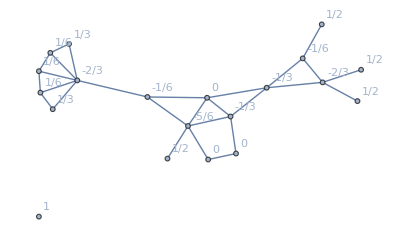

-Graphics-

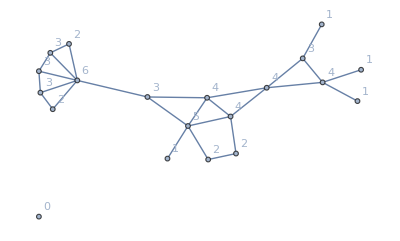

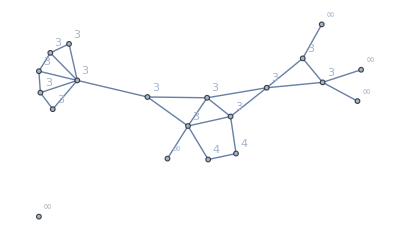

```mathematica
AdjacencyGraph[testg,VertexLabels->Table[i->cs[[i]],{i,20}]]
AdjacencyGraph[testg,VertexLabels->Table[i->cs[[i]],{i,20}]]
AdjacencyGraph[testg,VertexLabels->Table[i->degs[[i]],{i,20}]]
AdjacencyGraph[testg,VertexLabels->Table[i->cycs[[i]],{i,20}]]
```

```mathematica
EulerChi[testg]
```

1

```mathematica
Curvature[testg]
```

1

```mathematica
AvgDim[testg]
```

1801/1200

```mathematica
dtable=Table[Table[deg[g8u[[j]],i],{i,8}],{j,12346}];
ctable=Table[Table[MinCycle[g8u[[j]],i],{i,8}],{j,12346}];
```

```mathematica
Do[
Do[
If[(dtable[[i]]==dtable[[j]])&&(ctable[[i]]==ctable[[j]]),Print["i = ",i," j = ",j]],{j,i+1,12346}],{i,12346}]
```

i = 30 j = 107

i = 32 j = 108

i = 36 j = 113

i = 38 j = 114

i = 42 j = 119

i = 44 j = 120

i = 50 j = 129

i = 54 j = 136

i = 56 j = 139

i = 60 j = 208

i = 62 j = 146

i = 62 j = 210

i = 64 j = 149

i = 74 j = 248

i = 95 j = 131

i = 99 j = 141

i = 103 j = 151

i = 145 j = 209

i = 145 j = 1248

i = 146 j = 210

i = 148 j = 1249

i = 163 j = 355

i = 169 j = 402

i = 174 j = 236

i = 175 j = 361

i = 180 j = 250

i = 181 j = 422

i = 186 j = 258

i = 187 j = 367

i = 207 j = 1247

i = 209 j = 1248

i = 233 j = 404

i = 247 j = 418

i = 247 j = 1267

i = 255 j = 424

i = 259 j = 299

i = 260 j = 300

i = 269 j = 445

i = 277 j = 458

i = 277 j = 1306

i = 281 j = 461

i = 283 j = 465

i = 283 j = 501

i = 288 j = 320

i = 360 j = 408

i = 366 j = 428

i = 378 j = 443

i = 381 j = 447

i = 383 j = 481

i = 387 j = 463

i = 389 j = 1312

i = 390 j = 467

i = 392 j = 505

i = 409 j = 955

i = 417 j = 1266

i = 418 j = 1267

i = 429 j = 967

i = 442 j = 981

i = 446 j = 985

i = 452 j = 489

i = 458 j = 1306

i = 462 j = 1005

i = 465 j = 501

i = 466 j = 1009

i = 470 j = 580

i = 472 j = 513

i = 480 j = 987

i = 488 j = 1503

i = 504 j = 1011

i = 509 j = 578

i = 510 j = 604

i = 510 j = 1630

i = 511 j = 605

i = 512 j = 1511

i = 520 j = 938

i = 520 j = 1034

i = 523 j = 1224

i = 527 j = 1226

i = 531 j = 1230

i = 532 j = 745

i = 538 j = 1050

i = 540 j = 1052

i = 542 j = 1056

i = 543 j = 1386

i = 544 j = 782

i = 544 j = 943

i = 544 j = 1058

i = 544 j = 1661

i = 547 j = 1236

i = 549 j = 635

i = 551 j = 1238

i = 551 j = 1388

i = 552 j = 638

i = 553 j = 639

i = 555 j = 663

i = 555 j = 1242

i = 555 j = 1392

i = 556 j = 754

i = 560 j = 1264

i = 561 j = 1276

i = 567 j = 1283

i = 570 j = 1292

i = 595 j = 1304

i = 600 j = 1313

i = 600 j = 1626

i = 604 j = 1630

i = 607 j = 1318

i = 623 j = 1338

i = 636 j = 1603

i = 653 j = 671

$Aborted

```mathematica
dtable[[653]]
dtable[[671]]
ctable[[653]]
ctable[[671]]
```

{1,2,2,2,3,3,5,6}

{1,2,2,2,3,3,5,6}

{∞,3,3,4,3,3,3,3}

{∞,3,3,4,3,3,3,3}

```mathematica
IsomorphicGraphQ[AdjacencyGraph[g8u[[653]]],
AdjacencyGraph[g8u[[671]]]]
```

False

```mathematica
GraphPlot3D[AdjacencyGraph[g8u[[653]],VertexLabels->"Name"]]
GraphPlot3D[AdjacencyGraph[g8u[[671]],VertexLabels->"Name"]]
```

-Graphics3D-

-Graphics3D-

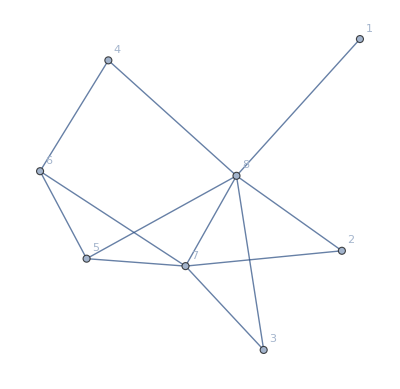

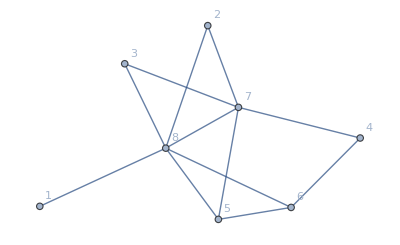

```mathematica
AdjacencyGraph[g8u[[653]],VertexLabels->"Name"]
AdjacencyGraph[g8u[[671]],VertexLabels->"Name"]
```

```mathematica
Curvatures[g8u[[653]]]
Curvatures[g8u[[671]]]
```

{1/2,1/3,1/3,0,1/6,-1/6,-1/6,-1}

{1/2,1/3,1/3,0,1/6,-1/6,-1/2,-2/3}

```mathematica
AllDims[g8u[[653]]]
AllDims[g8u[[671]]]
```

{1,2,2,1,2,5/3,2,5/3}

{1,2,2,1,2,5/3,9/5,11/6}

```mathematica
Union[{1,2,2,3},{1,1,2,4,5}]
```

{1,2,3,4,5}

```mathematica
Sort[{1,2,3,2}]==Sort[{3,1,2,2}]
```

True

#### Counting Graphs

```mathematica
g3=Makeensemble2[3];
Length[g3]==2^(Binomial[3,2])
g4=Makeensemble2[4];
Length[g4]==2^(Binomial[4,2])
g5=Makeensemble2[5];
Length[g5]==2^(Binomial[5,2])
```

Making graph 0

Making graph 2

Making graph 4

Making graph 6

True

Making graph 0

Making graph 16

Making graph 32

Making graph 48

True

Making graph 0

Making graph 256

Making graph 512

Making graph 768

True

```mathematica
count3=CountGraphs[g3,degs];
count4=CountGraphs[g4,degs];
count5=CountGraphs[g5,degs];
```

```mathematica
Sort[count3]
Sort[count4]
Sort[count5]
```

<|{0,0,0}→1,{2,2,2}→1,{0,1,1}→3,{1,1,2}→3|>

<|{0,0,0,0}→1,{3,3,3,3}→1,{1,1,1,1}→3,{2,2,2,2}→3,{1,1,1,3}→4,{0,2,2,2}→4,{0,0,1,1}→6,{2,2,3,3}→6,{0,1,1,2}→12,{1,1,2,2}→12,{1,2,2,3}→12|>

<|{0,0,0,0,0}→1,{4,4,4,4,4}→1,{1,1,1,1,4}→5,{0,3,3,3,3}→5,{0,0,0,1,1}→10,{0,0,2,2,2}→10,{2,2,2,4,4}→10,{3,3,4,4,4}→10,{2,2,2,2,2}→12,{0,1,1,1,1}→15,{0,2,2,2,2}→15,{2,2,2,2,4}→15,{3,3,3,3,4}→15,{0,1,1,1,3}→20,{1,3,3,3,4}→20,{0,0,1,1,2}→30,{1,1,1,1,2}→30,{1,1,2,2,4}→30,{0,2,2,3,3}→30,{2,3,3,3,3}→30,{2,3,3,4,4}→30,{0,1,1,2,2}→60,{0,1,2,2,3}→60,{1,1,1,2,3}→60,{1,1,2,3,3}→60,{1,2,2,3,4}→60,{1,2,3,3,3}→60,{2,2,3,3,4}→60,{1,1,2,2,2}→70,{2,2,2,3,3}→70,{1,2,2,2,3}→120|>

```mathematica
Dim[g3u[[1]],1]
```

0

## Speed Tests

```mathematica
boltzmanWeight[Amat_,J_,b_]:=Exp[-b*H0[Amat,J]];
```

```mathematica
DistributeDefinitions[boltzmanWeight]
DistributeDefinitions[H0]
DistributeDefinitions[AvgDim]
DistributeDefinitions[AvgDeg]
```

{}

{}

{}

«1 more identical outputs»

```mathematica
AbsoluteTiming[
bweights=ParallelMap[boltzmanWeight[#,1.0,0.1]&,g8u];
funcvals=ParallelMap[AvgDim,g8u];
expval=bweights.funcvals;
Pval=Total[bweights];
Fval=-Log[Pval]/0.1;
{Pval,Fval,expval}
]
```

{5.32181,{4648.1,-84.4421,9034.72}}

```mathematica
AbsoluteTiming[
bweights=Map[boltzmanWeight[#,1.0,0.1]&,g8u];
funcvals=Map[AvgDim,g8u];
expval=bweights.funcvals;
Pval=Total[bweights];
Fval=-Log[Pval]/0.1;
{Pval,Fval,expval}
]
```

{40.7131,{4648.1,-84.4421,9034.72}}

```mathematica
AbsoluteTiming[ParallelExpectationValue[g8u,AvgDim,H0[#,1.0]&,0.1]]
```

{5.98482,{4648.1,-84.4421,1.94375}}

```mathematica
$ProcessorCount
```

18

```mathematica
DistributeDefinitions[ParallelExpectationValue];
DistributeDefinitions[Dim];
AbsoluteTiming[ParallelExpectationValue[g9u,Dim[2],H0[1.0],0.0001]]
```

{51.1324,{9979.82,-92083.2,1.62324}}

## Exact Expectation values

H0

## N = 1

```mathematica
avdim1=ExpectationValue[g1u,AvgDim,H0Tot[J,L],b]
```

{1.,0.,0.}

```mathematica
avdeg1=ExpectationValue[g1u,AvgDeg,H0Tot[J,L],b]
```

{1.,0.,0.}

```mathematica
avK1=ExpectationValue[g1u,EulerChi,H0Tot[J,L],b]
```

{1.,0.,1.}

```mathematica
avdim1f[b_,J_,L_]=avdim1[[3]];
avdeg1f[b_,J_,L_]=avdeg1[[3]];
freeF1[b_,J_,L_]=avdeg1[[2]];
avK1f[b_,J_,L_]=avK1[[3]];
Magnetizationd1[b_,J_,L_]=D[freeF1[b,J,L],{L,1}]/1.0;
Chideg1[b_,J_,L_]=-D[Magnetizationd1[b,J,L],{L,1}]/(1.0*b);
delD1[b_,J_,L_]=D[freeF1[b,J,L],{J,1}]/1.0;(*the expectation value of the square of the total degree difference within a graph*)
```

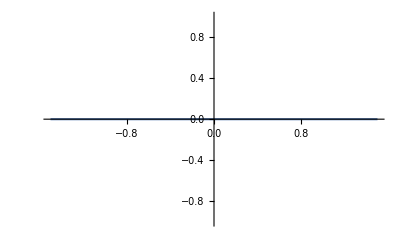

```mathematica
Plot[{Magnetizationd1[1.2,1.0,L],avdeg1f[1.0,L]},{L,-1.5,1.5}]
```

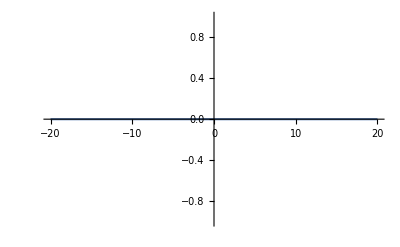

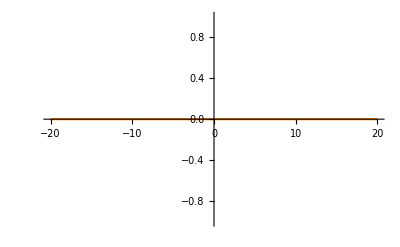

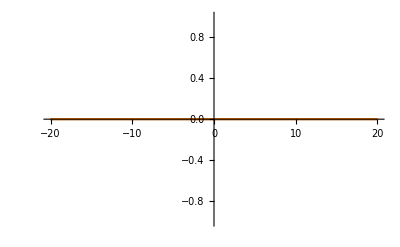

```mathematica
degplot1=Plot[avdeg1f[0.1,1.0,L],{L,-20,20},PlotRange->All]
dimplot1=Plot[avdim1f[0.1,1.0,L],{L,-20.0,20.0},PlotRange->All,PlotStyle->Orange]
Show[degplot1,dimplot1]
```

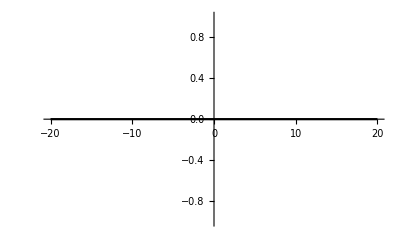

```mathematica
chidegplot1=Plot[{Chideg1[0.1,1.0,L]},{L,-20.0,20.0},PlotRange->All,PlotStyle->Black]
```

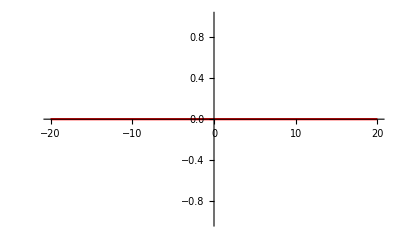

```mathematica
deldplot1=Plot[{delD1[0.1,1.0,L]},{L,-20.0,20.0},PlotRange->All,PlotStyle->Red]
```

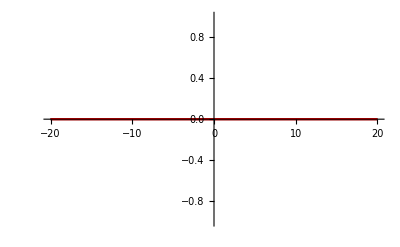

```mathematica
Show[chidegplot1,deldplot1]
```

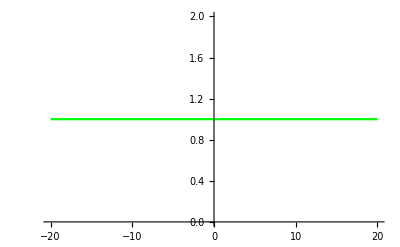

```mathematica
Clear[Kplot];Kplot1=Plot[{avK1f[0.1,1.0,L]/1.0},{L,-20.0,20.0},PlotRange->All,PlotStyle->Green]
```

```mathematica
Fplot1=Plot[freeF1[0.1,1.0,L],{L,-20,20},PlotRange->All]
```

-Graphics-

```mathematica
Energies[g1u,H0Tot[1.0,-1.0],1]
```

Now computing energy of graph 1

<|0.→{-Graphics-}|>

## N = 2

```mathematica
avdim2=ExpectationValue[g2u,AvgDim,H0Tot[J,L],b]
avdeg2=ExpectationValue[g2u,AvgDeg,H0Tot[J,L],b]
avK2=ExpectationValue[g2u,EulerChi,H0Tot[J,L],b]
avdim2f[b_,J_,L_]=avdim2[[3]];
avdeg2f[b_,J_,L_]=avdeg2[[3]];
freeF2[b_,J_,L_]=avdeg2[[2]];
avK2f[b_,J_,L_]=avK2[[3]];
Magnetizationd2[b_,J_,L_]=D[freeF2[b,J,L],{L,1}]/2.0;
Chideg2[b_,J_,L_]=-D[Magnetizationd2[b,J,L],{L,1}]/(2.0*b);
delD2[b_,J_,L_]=D[freeF2[b,J,L],{J,1}]/2.0;(*the expectation value of the square of the total degree difference within a graph*)
```

{1.+ⅇ^(-b (0.+2 L)),-Log[1.+ⅇ^(-b (0.+2 L))]/b,(1. (0.+ⅇ^(-b (0.+2 L))))/(1.+ⅇ^(-b (0.+2 L)))}

{1.+ⅇ^(-b (0.+2 L)),-Log[1.+ⅇ^(-b (0.+2 L))]/b,(1. (0.+ⅇ^(-b (0.+2 L))))/(1.+ⅇ^(-b (0.+2 L)))}

{1.+ⅇ^(-b (0.+2 L)),-Log[1.+ⅇ^(-b (0.+2 L))]/b,(1. (2.+ⅇ^(-b (0.+2 L))))/(1.+ⅇ^(-b (0.+2 L)))}

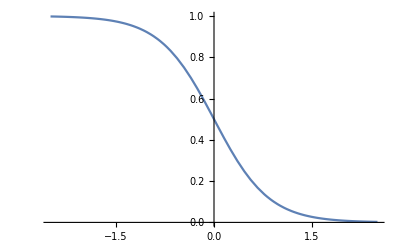

```mathematica
Plot[{Magnetizationd2[1.2,1.0,L],avdeg2f[1.0,L]},{L,-2.5,2.5},PlotRange->All]
```

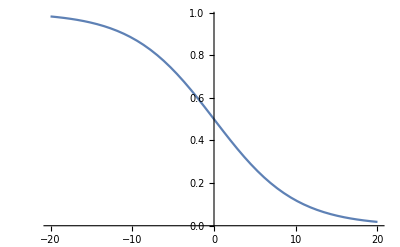

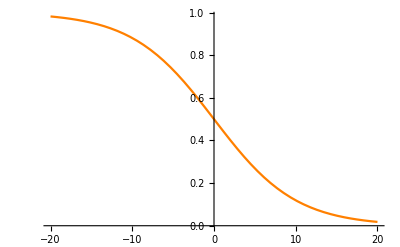

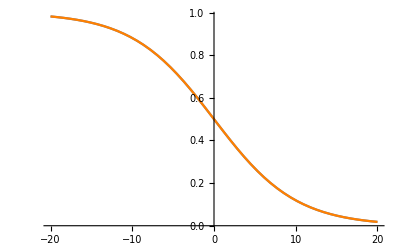

```mathematica
degplot2=Plot[avdeg2f[0.1,1.0,L],{L,-20,20},PlotRange->All]
dimplot2=Plot[avdim2f[0.1,1.0,L],{L,-20.0,20.0},PlotRange->All,PlotStyle->Orange]
Show[degplot2,dimplot2]
```

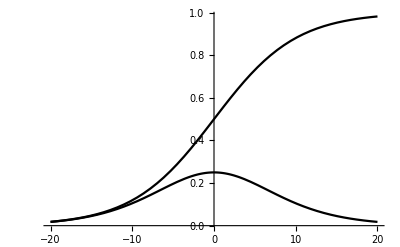

```mathematica
chidegplot2=Plot[{Chideg2[0.1,1.0,L],Chideg2[0.1,1.0,L]/avdeg2f[0.1,1.0,L]},{L,-20.0,20.0},PlotRange->All,PlotStyle->Black]
```

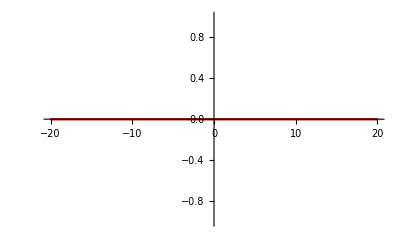

```mathematica
deldplot2=Plot[{delD2[0.1,1.0,L],delD2[0.1,1.0,L]/avdeg2f[0.1,1.0,L]},{L,-20.0,20.0},PlotRange->All,PlotStyle->Red]
```

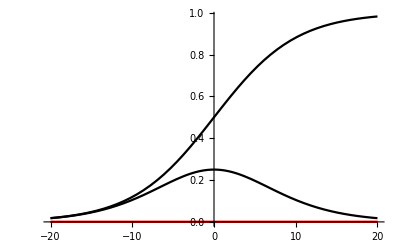

```mathematica
Show[chidegplot2,deldplot2]
```

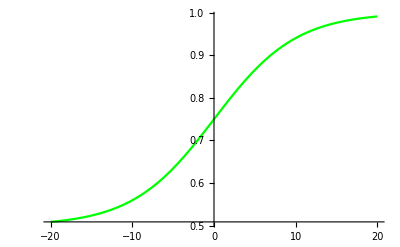

```mathematica
Kplot2=Plot[{avK2f[0.1,1.0,L]/2.0},{L,-20.0,20.0},PlotRange->All,PlotStyle->Green]
```

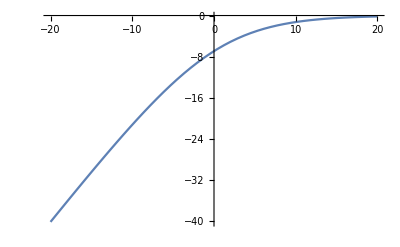

```mathematica
Fplot2=Plot[freeF2[0.1,1.0,L],{L,-20,20},PlotRange->All]
```

```mathematica
Energies[g2u,H0Tot[1.0,-1.0],1]
```

Now computing energy of graph 1

Now computing energy of graph 2

<|-2.→{-Graphics-}|>

## N = 3

```mathematica
avdim3=ExpectationValue[g3u,AvgDim,H0Tot[J,L],b]
avdeg3=ExpectationValue[g3u,AvgDeg,H0Tot[J,L],b]
avK3=ExpectationValue[g3u,EulerChi,H0Tot[J,L],b]
avdim3f[b_,J_,L_]=avdim3[[3]];
avdeg3f[b_,J_,L_]=avdeg3[[3]];
freeF3[b_,J_,L_]=avdeg3[[2]];
avK3f[b_,J_,L_]=avK3[[3]];
Magnetizationd3[b_,J_,L_]=D[freeF3[b,J,L],{L,1}]/3.0;
Chideg3[b_,J_,L_]=-D[Magnetizationd3[b,J,L],{L,1}]/(3.0*b);
delD3[b_,J_,L_]=D[freeF3[b,J,L],{J,1}]/3.0;(*the expectation value of the square of the total degree difference within a graph*)
```

{1.+ⅇ^(-b (0.666667 J+2 L))+ⅇ^(-b (0.666667 J+4 L))+ⅇ^(-b (0.+6 L)),-Log[1.+ⅇ^(-b (0.666667 J+2 L))+ⅇ^(-b (0.666667 J+4 L))+ⅇ^(-b (0.+6 L))]/b,(1. (0.+2/3 ⅇ^(-b (0.666667 J+2 L))+ⅇ^(-b (0.666667 J+4 L))+2 ⅇ^(-b (0.+6 L))))/(1.+ⅇ^(-b (0.666667 J+2 L))+ⅇ^(-b (0.666667 J+4 L))+ⅇ^(-b (0.+6 L)))}

{1.+ⅇ^(-b (0.666667 J+2 L))+ⅇ^(-b (0.666667 J+4 L))+ⅇ^(-b (0.+6 L)),-Log[1.+ⅇ^(-b (0.666667 J+2 L))+ⅇ^(-b (0.666667 J+4 L))+ⅇ^(-b (0.+6 L))]/b,(1. (0.+2/3 ⅇ^(-b (0.666667 J+2 L))+4/3 ⅇ^(-b (0.666667 J+4 L))+2 ⅇ^(-b (0.+6 L))))/(1.+ⅇ^(-b (0.666667 J+2 L))+ⅇ^(-b (0.666667 J+4 L))+ⅇ^(-b (0.+6 L)))}

{1.+ⅇ^(-b (0.666667 J+2 L))+ⅇ^(-b (0.666667 J+4 L))+ⅇ^(-b (0.+6 L)),-Log[1.+ⅇ^(-b (0.666667 J+2 L))+ⅇ^(-b (0.666667 J+4 L))+ⅇ^(-b (0.+6 L))]/b,(1. (3.+2 ⅇ^(-b (0.666667 J+2 L))+ⅇ^(-b (0.666667 J+4 L))+ⅇ^(-b (0.+6 L))))/(1.+ⅇ^(-b (0.666667 J+2 L))+ⅇ^(-b (0.666667 J+4 L))+ⅇ^(-b (0.+6 L)))}

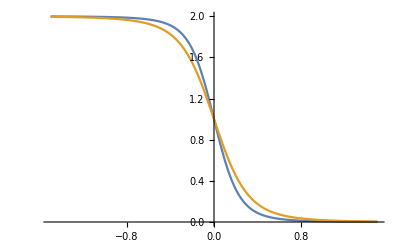

```mathematica
Plot[{Magnetizationd3[1.8,1.0,L],avdeg3f[1.4,1.0,L]},{L,-1.5,1.5},PlotRange->All]
```

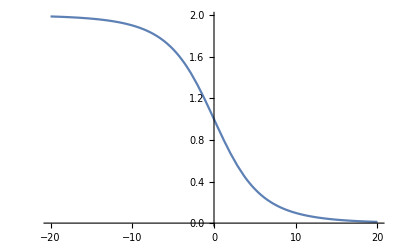

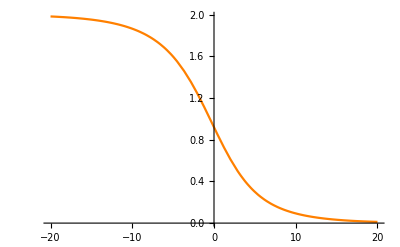

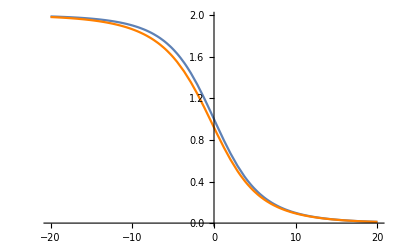

```mathematica
degplot3=Plot[avdeg3f[0.1,1.0,L],{L,-20,20},PlotRange->All]
dimplot3=Plot[avdim3f[0.1,1.0,L],{L,-20.0,20.0},PlotRange->All,PlotStyle->Orange]
Show[degplot3,dimplot3]
```

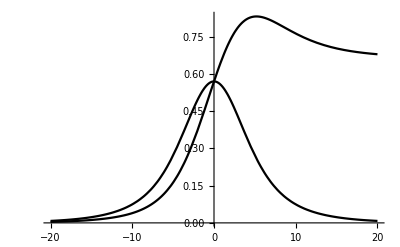

```mathematica
chidegplot3=Plot[{Chideg3[0.1,1.0,L],Chideg3[0.1,1.0,L]/avdeg3f[0.1,1.0,L]},{L,-20.0,20.0},PlotRange->All,PlotStyle->Black]
```

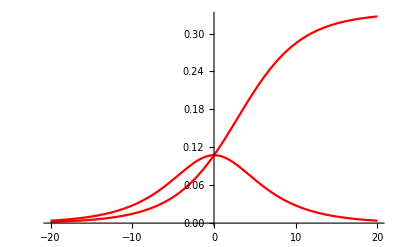

```mathematica
deldplot3=Plot[{delD3[0.1,1.0,L],delD3[0.1,1.0,L]/avdeg3f[0.1,1.0,L]},{L,-20.0,20.0},PlotRange->All,PlotStyle->Red]
```

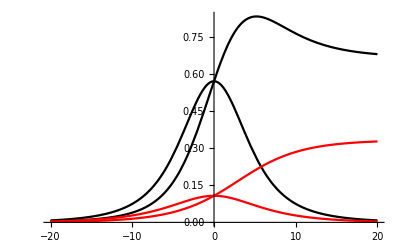

```mathematica
Show[chidegplot3,deldplot3]
```

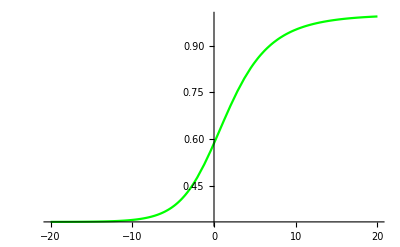

```mathematica
Kplot3=Plot[{avK3f[0.1,1.0,L]/3.0},{L,-20.0,20.0},PlotRange->All,PlotStyle->Green]
```

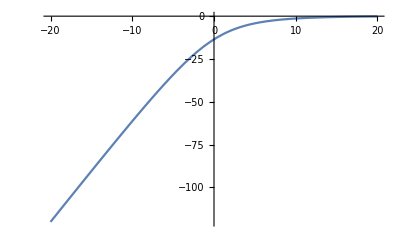

```mathematica
Fplot3=Plot[freeF3[0.1,1.0,L],{L,-20,20},PlotRange->All]
```

```mathematica
Energies[g3u,H0Tot[1.0,-1.0],3]
```

Now computing energy of graph 2

Now computing energy of graph 4

<|-6.→{-Graphics-},-3.33333→{-Graphics-},-1.33333→{-Graphics-}|>

## N = 4

```mathematica
avdim4=ExpectationValue[g4u,AvgDim,H0Tot[J,L],b];
avdeg4=ExpectationValue[g4u,AvgDeg,H0Tot[J,L],b];
avK4=ExpectationValue[g4u,EulerChi,H0Tot[J,L],b];
avdim4f[b_,J_,L_]=avdim4[[3]];
avdeg4f[b_,J_,L_]=avdeg4[[3]];
freeF4[b_,J_,L_]=avdeg4[[2]];
avK4f[b_,J_,L_]=avK4[[3]];
Magnetizationd4[b_,J_,L_]=D[freeF4[b,J,L],{L,1}]/4.0;
Chideg4[b_,J_,L_]=-D[Magnetizationd4[b,J,L],{L,1}]/(4.0*b);
delD4[b_,J_,L_]=D[freeF4[b,J,L],{J,1}]/4.0;(*the expectation value of the square of the total degree difference within a graph*)
```

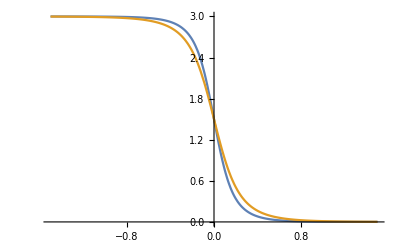

```mathematica
Plot[{Magnetizationd4[1.8,1.0,L],avdeg4f[1.4,1.0,L]},{L,-1.5,1.5},PlotRange->All]
```

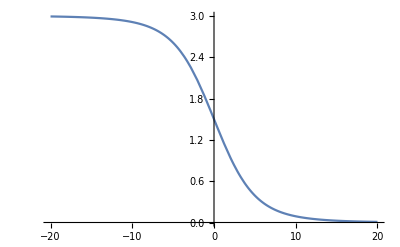

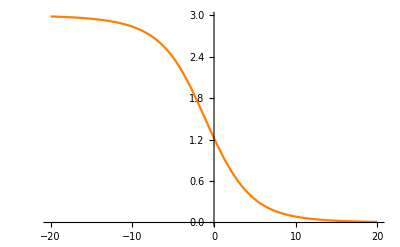

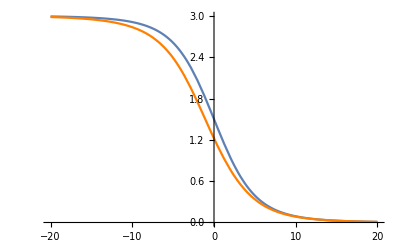

```mathematica
degplot4=Plot[avdeg4f[0.1,1.0,L],{L,-20,20},PlotRange->All]
dimplot4=Plot[avdim4f[0.1,1.0,L],{L,-20.0,20.0},PlotRange->All,PlotStyle->Orange]
Show[degplot4,dimplot4]
```

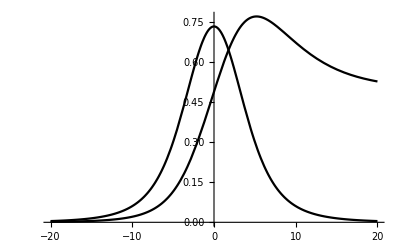

```mathematica
chidegplot4=Plot[{Chideg4[0.1,1.0,L],Chideg4[0.1,1.0,L]/avdeg4f[0.1,1.0,L]},{L,-20.0,20.0},PlotRange->All,PlotStyle->Black]
```

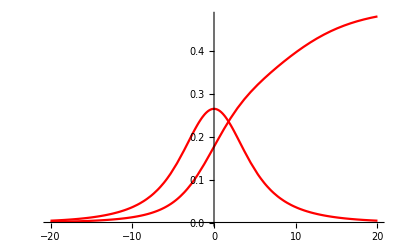

```mathematica
deldplot4=Plot[{delD4[0.1,1.0,L],delD4[0.1,1.0,L]/avdeg4f[0.1,1.0,L]},{L,-20.0,20.0},PlotRange->All,PlotStyle->Red]
```

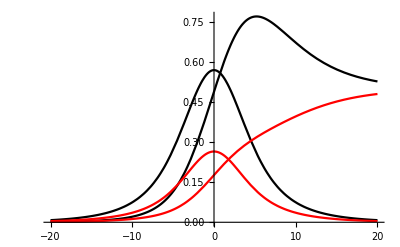

```mathematica
Show[chidegplot4,deldplot4]
```

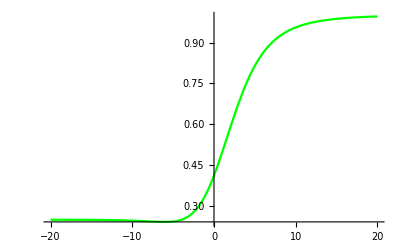

```mathematica
Kplot4=Plot[{avK4f[0.1,1.0,L]/4.0},{L,-20.0,20.0},PlotRange->All,PlotStyle->Green]
```

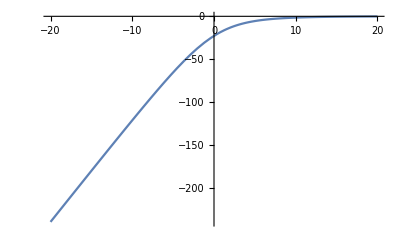

```mathematica
Fplot4=Plot[freeF4[0.1,1.0,L],{L,-20,20},PlotRange->All]
```

```mathematica
AbsoluteTiming[Energies[g4u,H0Tot[1.0,-1.0],5]]
```

Now computing energy of graph 11

{0.002913,<|-12.→{-Graphics-},-9.→{-Graphics-},-8.→{-Graphics-},-6.→{-Graphics-},-5.→{-Graphics-}|>}

## N = 5

```mathematica
avdim5=ExpectationValue[g5u,AvgDim,H0Tot[J,L],b];
avdeg5=ExpectationValue[g5u,AvgDeg,H0Tot[J,L],b];
avK5=ExpectationValue[g5u,EulerChi,H0Tot[J,L],b];
avdim5f[b_,J_,L_]=avdim5[[3]];
avdeg5f[b_,J_,L_]=avdeg5[[3]];
freeF5[b_,J_,L_]=avdeg5[[2]];
avK5f[b_,J_,L_]=avK5[[3]];
Magnetizationd5[b_,J_,L_]=D[freeF5[b,J,L],{L,1}]/5.0;
Chideg5[b_,J_,L_]=-D[Magnetizationd5[b,J,L],{L,1}]/(5.0*b);
delD5[b_,J_,L_]=D[freeF5[b,J,L],{J,1}]/5.0;(*the expectation value of the square of the total degree difference within a graph*)
```

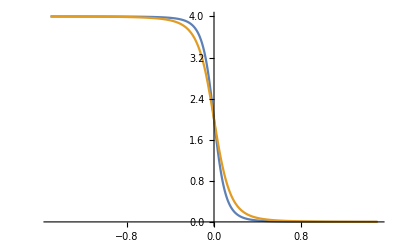

```mathematica
Plot[{Magnetizationd5[1.8,1.0,L],avdeg5f[1.4,1.0,L]},{L,-1.5,1.5},PlotRange->All]
```

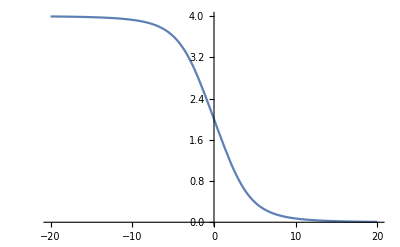

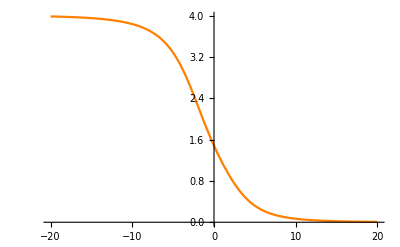

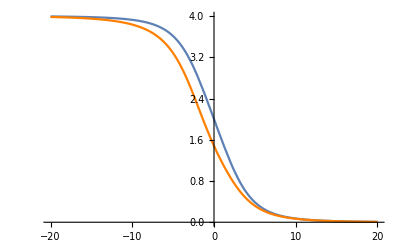

```mathematica
degplot5=Plot[avdeg5f[0.1,1.0,L],{L,-20,20},PlotRange->All]
dimplot5=Plot[avdim5f[0.1,1.0,L],{L,-20.0,20.0},PlotRange->All,PlotStyle->Orange]
Show[degplot5,dimplot5]
```

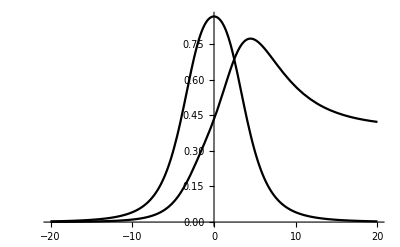

```mathematica
chidegplot5=Plot[{Chideg5[0.1,1.0,L],Chideg5[0.1,1.0,L]/avdeg5f[0.1,1.0,L]},{L,-20.0,20.0},PlotRange->All,PlotStyle->Black]
```

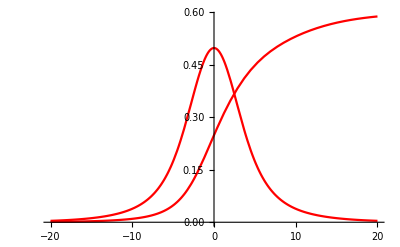

```mathematica
deldplot5=Plot[{delD5[0.1,1.0,L],delD5[0.1,1.0,L]/avdeg5f[0.1,1.0,L]},{L,-20.0,20.0},PlotRange->All,PlotStyle->Red]
```

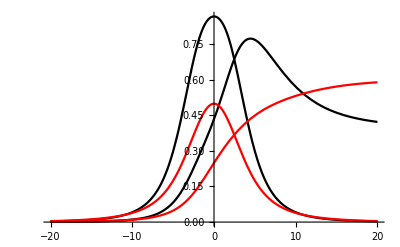

```mathematica
Show[chidegplot5,deldplot5]
```

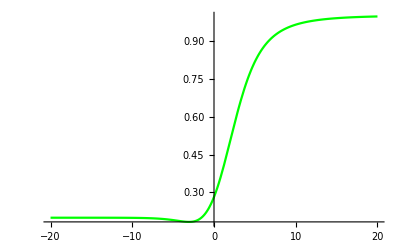

```mathematica
Kplot5=Plot[{avK5f[0.1,1.0,L]/5.0},{L,-20.0,20.0},PlotRange->All,PlotStyle->Green]
```

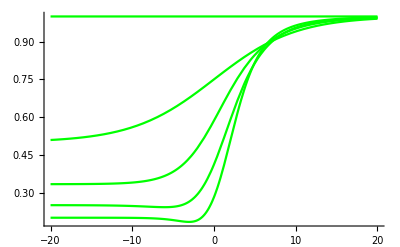

```mathematica
Show[Kplot1,Kplot2,Kplot3,Kplot4,Kplot5]
```

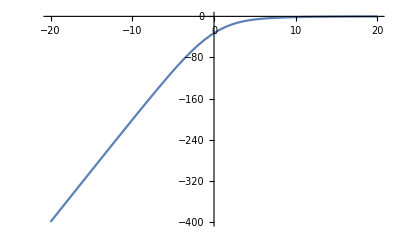

```mathematica
Fplot5=Plot[freeF5[0.1,1.0,L],{L,-20,20},PlotRange->All]
```

```mathematica
AbsoluteTiming[Energies[g5u,H0Tot[1.0,-1.0],5]]
```

Now computing energy of graph 17

Now computing energy of graph 34

{0.00891,<|-20.→{-Graphics-},-16.8→{-Graphics-},-15.2→{-Graphics-},-13.2→{-Graphics-,-Graphics-},-11.2→{-Graphics-}|>}

## N = 6

```mathematica
avdim6=ExpectationValue[g6u,AvgDim,H0Tot[J,L],b];
avdeg6=ExpectationValue[g6u,AvgDeg,H0Tot[J,L],b];
avK6=ExpectationValue[g6u,EulerChi,H0Tot[J,L],b];
avdim6f[b_,J_,L_]=avdim6[[3]];
avdeg6f[b_,J_,L_]=avdeg6[[3]];
freeF6[b_,J_,L_]=avdeg6[[2]];
avK6f[b_,J_,L_]=avK6[[3]];
Magnetizationd6[b_,J_,L_]=D[freeF6[b,J,L],{L,1}]/6.0;
Chideg6[b_,J_,L_]=-D[Magnetizationd6[b,J,L],{L,1}]/(6.0*b);
delD6[b_,J_,L_]=D[freeF6[b,J,L],{J,1}]/6.0;(*the expectation value of the square of the total degree difference within a graph*)
```

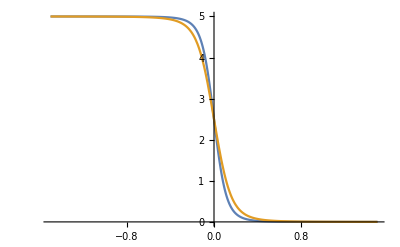

```mathematica
Plot[{Magnetizationd6[1.8,1.0,L],avdeg6f[1.4,1.0,L]},{L,-1.5,1.5},PlotRange->All]
```

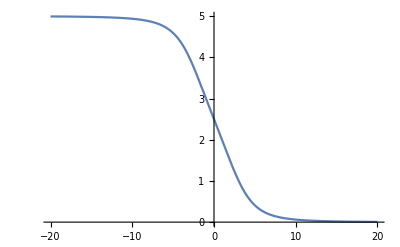

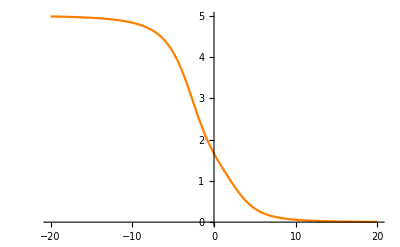

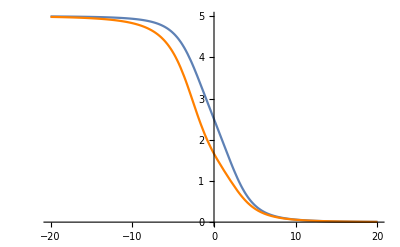

```mathematica
degplot6=Plot[avdeg6f[0.1,1.0,L],{L,-20,20},PlotRange->All]
dimplot6=Plot[avdim6f[0.1,1.0,L],{L,-20.0,20.0},PlotRange->All,PlotStyle->Orange]
Show[degplot6,dimplot6]
```

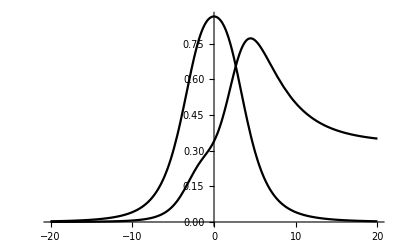

```mathematica
chidegplot6=Plot[{Chideg5[0.1,1.0,L],Chideg6[0.1,1.0,L]/avdeg6f[0.1,1.0,L]},{L,-20.0,20.0},PlotRange->All,PlotStyle->Black]
```

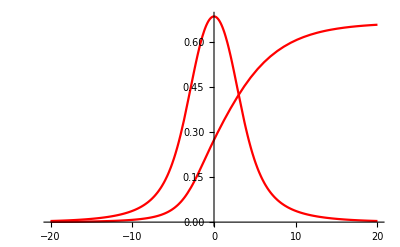

```mathematica
deldplot6=Plot[{delD6[0.1,1.0,L],delD6[0.1,1.0,L]/avdeg6f[0.1,1.0,L]},{L,-20.0,20.0},PlotRange->All,PlotStyle->Red]
```

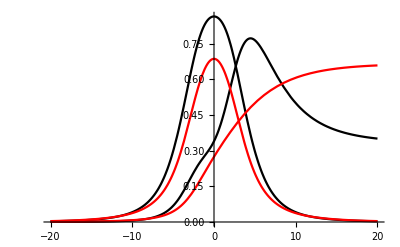

```mathematica
Show[chidegplot6,deldplot6]
```

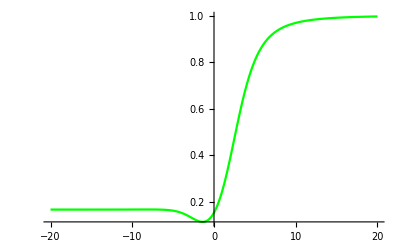

```mathematica
Kplot6=Plot[{avK6f[0.1,1.0,L]/6.0},{L,-20.0,20.0},PlotRange->All,PlotStyle->Green]
```

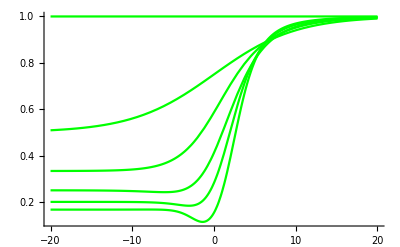

```mathematica
Show[Kplot1,Kplot2,Kplot3,Kplot4,Kplot5,Kplot6]
```

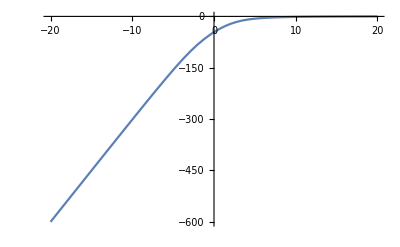

```mathematica
Fplot6=Plot[freeF6[0.1,1.0,L],{L,-20,20},PlotRange->All]
```

```mathematica
Energies[g6u,H0Tot[1.0,-1.0],8]
```

Now computing energy of graph 78

Now computing energy of graph 156

<|-30.→{-Graphics-},-26.6667→{-Graphics-},-24.6667→{-Graphics-},-24.→{-Graphics-},-22.6667→{-Graphics-},-22.→{-Graphics-},-20.6667→{-Graphics-,-Graphics-},-20.→{-Graphics-}|>

```mathematica
GraphPlot3D[-Graphics-,ImageSize->Large]
```

-Graphics3D-

```mathematica
Dims[Normal[AdjacencyMatrix[-Graphics-]]]
AvgDim[Normal[AdjacencyMatrix[-Graphics-]]]
```

{3,3,3,3,3,3}

3

```mathematica
Valencyvec[Normal[AdjacencyMatrix[-Graphics-]]]
```

{3,3,4,4,5,5}

```mathematica
Curvatures[Normal[AdjacencyMatrix[-Graphics-]]]
GCurvature[Normal[AdjacencyMatrix[-Graphics-]]]
```

{1/4,1/4,1/6,1/6,1/12,1/12}

1

## N = 7

```mathematica
avdim7=ExpectationValue[g7u,AvgDim,H0Tot[J,L],b];
```

```mathematica
avdeg7=ExpectationValue[g7u,AvgDeg,H0Tot[J,L],b];
```

```mathematica
avK7=ExpectationValue[g7u,EulerChi,H0Tot[J,L],b];
```

```mathematica
avdim7f[b_,J_,L_]=avdim7[[3]];
avdeg7f[b_,J_,L_]=avdeg7[[3]];
freeF7[b_,J_,L_]=avdeg7[[2]];
avK7f[b_,J_,L_]=avK7[[3]];
Magnetizationd7[b_,J_,L_]=D[freeF7[b,J,L],{L,1}]/7.0;
Chideg7[b_,J_,L_]=-D[Magnetizationd7[b,J,L],{L,1}]/(7.0*b);
delD7[b_,J_,L_]=D[freeF7[b,J,L],{J,1}]/7.0;(*the expectation value of the square of the total degree difference within a graph*)
```

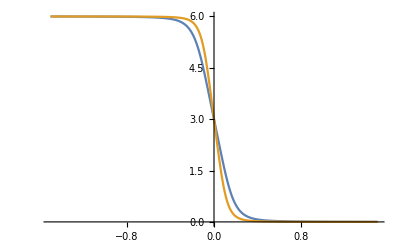

```mathematica
Plot[{Magnetizationd7[1.2,1.0,L],avdeg7f[1.6,1.0,L]},{L,-1.5,1.5},PlotRange->All]
```

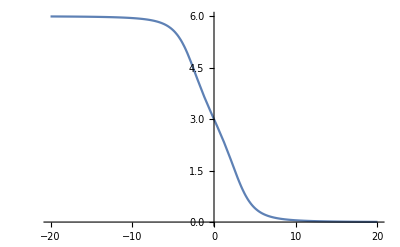

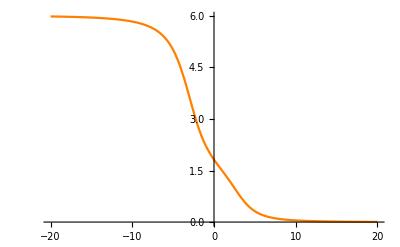

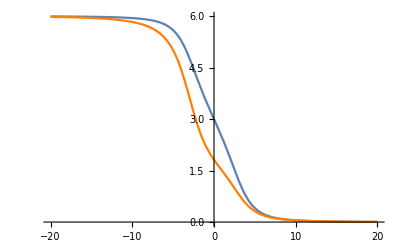

```mathematica
degplot7=Plot[avdeg7f[0.1,1.0,L],{L,-20,20},PlotRange->All]
dimplot7=Plot[avdim7f[0.1,1.0,L],{L,-20.0,20.0},PlotRange->All,PlotStyle->Orange]
Show[degplot7,dimplot7]
```

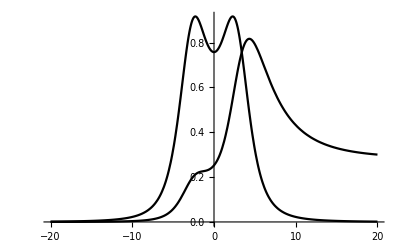

```mathematica
chidegplot7=Plot[{Chideg7[0.1,1.0,L],Chideg7[0.1,1.0,L]/avdeg7f[0.1,1.0,L]},{L,-20.0,20.0},PlotRange->All,PlotStyle->Black]
```

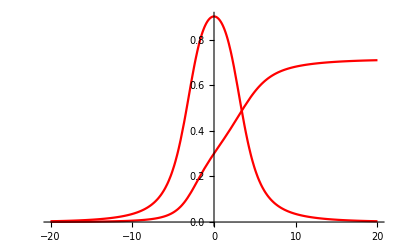

```mathematica
deldplot7=Plot[{delD7[0.1,1.0,L],delD7[0.1,1.0,L]/avdeg7f[0.1,1.0,L]},{L,-20.0,20.0},PlotRange->All,PlotStyle->Red]
```

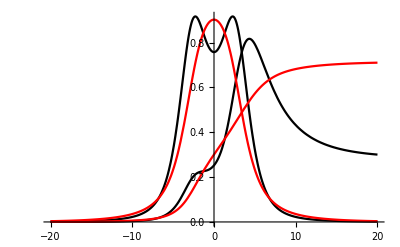

```mathematica
Show[chidegplot7,deldplot7]
```

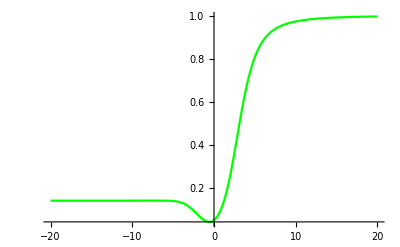

```mathematica
Kplot7=Plot[{avK7f[0.1,1.0,L]/7.0},{L,-20.0,20.0},PlotRange->All,PlotStyle->Green]
```

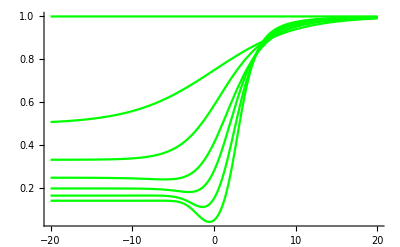

```mathematica
Show[Kplot1,Kplot2,Kplot3,Kplot4,Kplot5,Kplot6,Kplot7]
```

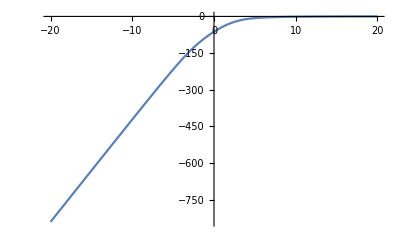

```mathematica
Fplot7=Plot[freeF7[0.1,1.0,L],{L,-20,20},PlotRange->All]
```

```mathematica
Energies[g7u,H0Tot[1.0,-1.0],8]
```

Now computing energy of graph 522

Now computing energy of graph 1044

<|-42.→{-Graphics-},-38.5714→{-Graphics-},-36.2857→{-Graphics-},-35.1429→{-Graphics-},-34.2857→{-Graphics-},-33.1429→{-Graphics-,-Graphics-},-31.1429→{-Graphics-,-Graphics-,-Graphics-},-30.2857→{-Graphics-,-Graphics-,-Graphics-}|>

```mathematica
GraphPlot3D[-Graphics-,ImageSize->{70,70}]
```

-Graphics3D-

```mathematica
AvgDim[Normal[AdjacencyMatrix[-Graphics-]]]
Dims[Normal[AdjacencyMatrix[-Graphics-]]]
Valencyvec[Normal[AdjacencyMatrix[-Graphics-]]]
```

3

{3,3,3,3,3,3,3}

{5,5,5,5,5,5,6}

```mathematica
Curvatures[Normal[AdjacencyMatrix[-Graphics-]]]
GCurvature[Normal[AdjacencyMatrix[-Graphics-]]]
EulerChi[Normal[AdjacencyMatrix[-Graphics-]]]
```

{1/6,1/6,1/6,1/6,1/6,1/6,0}

1

1

## N = 8

```mathematica
avdim8=ExpectationValue[g8u,AvgDim,H0Tot[J,L],b];
```

```mathematica
avdeg8=ExpectationValue[g8u,AvgDeg,H0Tot[J,L],b];
```

```mathematica
avK8=ExpectationValue[g8u,EulerChi,H0Tot[J,L],b];
```

```mathematica
Magnetizationd8[b_,J_,L_]=D[freeF8[b,J,L],{L,1}]/8.0;
Chideg8[b_,J_,L_]=-D[Magnetizationd8[b,J,L],{L,1}]/(8.0*b);
```

```mathematica
delD8[b_,J_,L_]=D[freeF8[b,J,L],{J,1}]/8.0;(*the expectation value of the square of the total degree difference within a graph*)
```

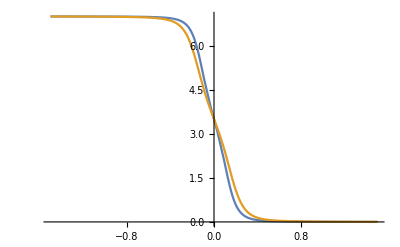

```mathematica
Plot[{Magnetizationd8[1.2,1.0,L],avdeg8f[1.0,1.0,L]},{L,-1.5,1.5},PlotRange->All]
```

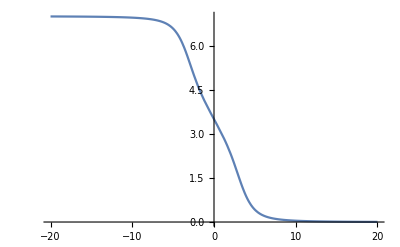

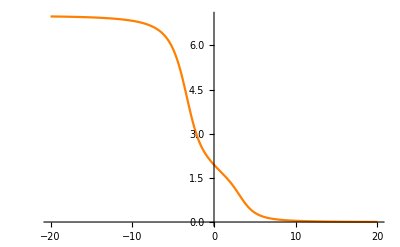

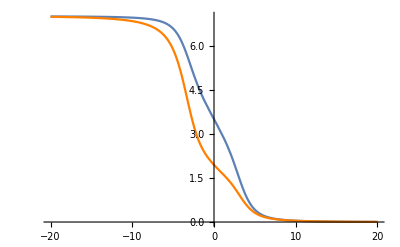

```mathematica
degplot8=Plot[avdeg8f[0.1,1.0,L],{L,-20,20},PlotRange->All]
dimplot8=Plot[avdim8f[0.1,1.0,L],{L,-20.0,20.0},PlotRange->All,PlotStyle->Orange]
Show[degplot8,dimplot8]
```

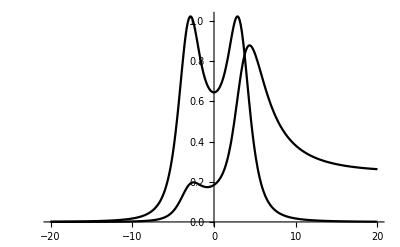

```mathematica
chidegplot8=Plot[{Chideg8[0.1,1.0,L],Chideg8[0.1,1.0,L]/avdeg8f[0.1,1.0,L]},{L,-20.0,20.0},PlotRange->All,PlotStyle->Black]
```

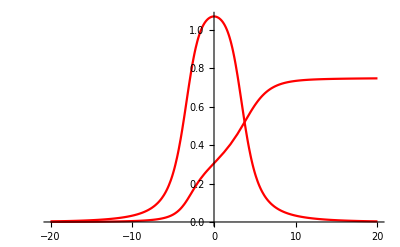

```mathematica
deldplot8=Plot[{delD8[0.1,1.0,L],delD8[0.1,1.0,L]/avdeg8f[0.1,1.0,L]},{L,-20.0,20.0},PlotRange->All,PlotStyle->Red]
```

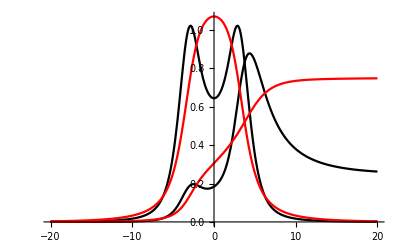

```mathematica
Show[chidegplot8,deldplot8]
```

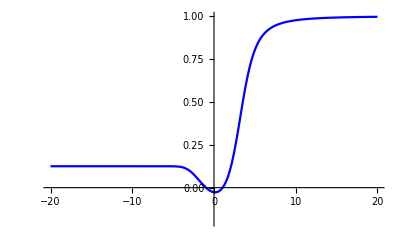

```mathematica
Kplot8=Plot[{avK8f[0.1,1.0,L]/8.0},{L,-20.0,20.0},PlotRange->{-0.2,1},PlotStyle->Blue]
```

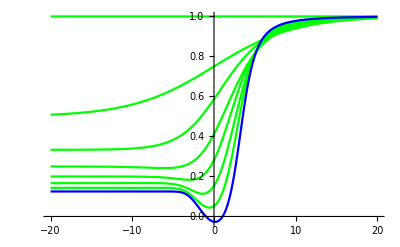

```mathematica
Show[Kplot1,Kplot2,Kplot3,Kplot4,Kplot5,Kplot6,Kplot7,Kplot8]
```

```mathematica
EulerChi[MakeKn[8]]
```

1

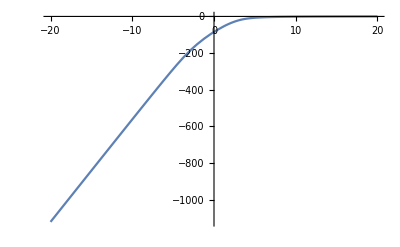

```mathematica
Fplot8=Plot[freeF8[0.1,1.0,L],{L,-20,20},PlotRange->All]
```

```mathematica
Energies[g8u,H0Tot[1.0,-1.0],12]
```

Now computing energy of graph 6173

Now computing energy of graph 12346

<|-56.→{-Graphics-},-52.5→{-Graphics-},-50.→{-Graphics-},-48.5→{-Graphics-},-48.→{-Graphics-,-Graphics-},-46.5→{-Graphics-},-46.→{-Graphics-},-44.5→{-Graphics-,-Graphics-,-Graphics-},-44.→{-Graphics-,-Graphics-},-42.5→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},-42.→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},-40.5→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}|>

```mathematica
GraphPlot3D[-Graphics-,ImageSize->Medium,EdgeRenderingFunction->({Cylinder[#1,0.05]}&),VertexRenderingFunction->({Sphere[#,0.1]}&)]
```

-Graphics3D-

```mathematica
Dims[Normal[AdjacencyMatrix[-Graphics-]]]
AvgDim[Normal[AdjacencyMatrix[-Graphics-]]]
Valencyvec[Normal[AdjacencyMatrix[-Graphics-]]]
```

{2,2,2,2,2,2,2,2}

2

{5,5,5,5,5,5,6,6}

```mathematica
Curvatures[Normal[AdjacencyMatrix[-Graphics-]]]
GCurvature[Normal[AdjacencyMatrix[-Graphics-]]]
```

{1/2,1/2,1/2,1/2,1/2,1/2,1,1}

5

## N = 9

```mathematica
(*avdim9=ExpectationValue[g9u,AvgDim,H0Tot[J,L],b];
```

```mathematica
(*avdeg9=ExpectationValue[g9u,AvgDeg,H0Tot[J,L],b];
```

Working on energy of graph 137334

Working on energy of graph 274668

Working on function value of graph = 137334

Working on function value of graph = 274668

```mathematica
(*avK9=ExpectationValue[g9u,EulerChi,H0Tot[J,L],b];
```

Working on energy of graph 100000

Working on energy of graph 200000

Working on function value of graph = 100000

Working on function value of graph = 200000

```mathematica
(*avdim9f[b_,J_,L_]=avdim9[[3]];*)
```

```mathematica
(*avdeg9f[b_,J_,L_]=avdeg9[[3]];*)
```

```mathematica
(*freeF9[b_,J_,L_]=avdeg9[[2]];*)
```

```mathematica
(*avK9f[b_,J_,L_]=avK9[[3]];*)
```

```mathematica
Magnetizationd9[b_,J_,L_]=D[freeF9[b,J,L],{L,1}]/9.0;
Chideg9[b_,J_,L_]=-D[Magnetizationd9[b,J,L],{L,1}]/(9.0*b);
```

```mathematica
delD9[b_,J_,L_]=D[freeF9[b,J,L],{J,1}]/9.0;(*the expectation value of the square of the total degree difference within a graph*)
```

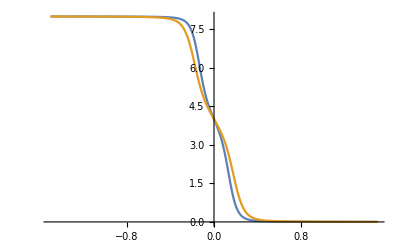

```mathematica
Plot[{Magnetizationd9[1.2,1.0,L],avdeg9f[1.0,1.0,L]},{L,-1.5,1.5},PlotRange->All]
```

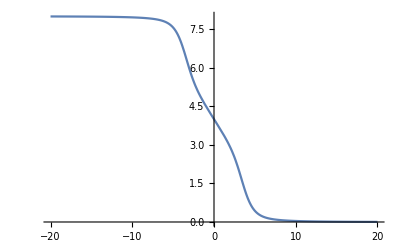

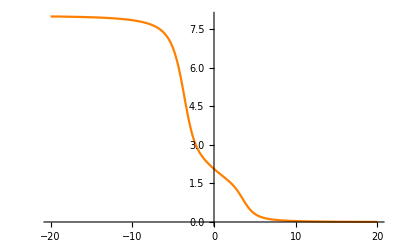

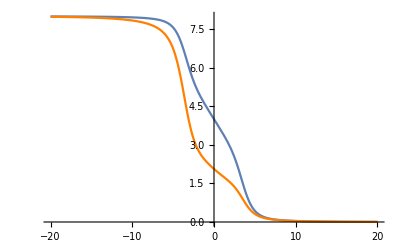

```mathematica
degplot9=Plot[avdeg9f[0.1,1.0,L],{L,-20,20},PlotRange->All]
dimplot9=Plot[avdim9f[0.1,1.0,L],{L,-20.0,20.0},PlotRange->All,PlotStyle->Orange]
Show[degplot9,dimplot9]
```

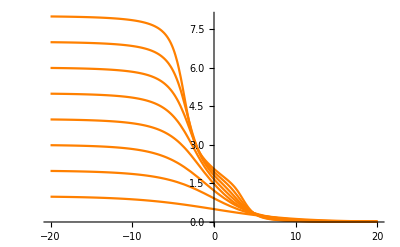

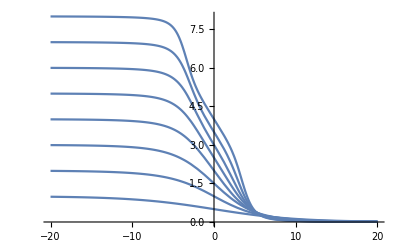

```mathematica
Show[dimplot2,dimplot3,dimplot4,dimplot5,dimplot6,dimplot7,dimplot8,dimplot9]
Show[degplot2,degplot3,degplot4,degplot5,degplot6,degplot7,degplot8,degplot9]
```

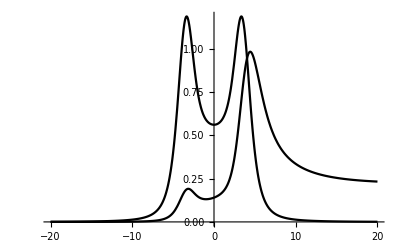

```mathematica
chidegplot9=Plot[{Chideg9[0.1,1.0,L],Chideg9[0.1,1.0,L]/avdeg9f[0.1,1.0,L]},{L,-20.0,20.0},PlotRange->All,PlotStyle->Black]
```

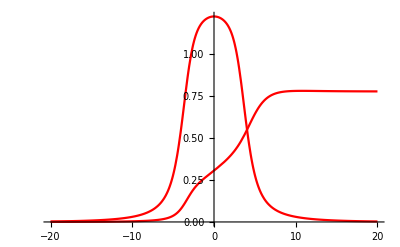

```mathematica
deldplot9=Plot[{delD9[0.1,1.0,L],delD9[0.1,1.0,L]/avdeg9f[0.1,1.0,L]},{L,-20.0,20.0},PlotRange->All,PlotStyle->Red]
```

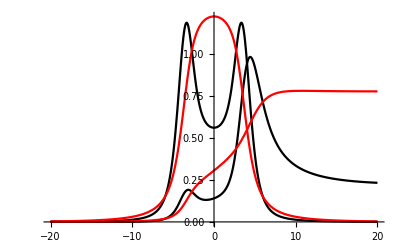

```mathematica
Show[chidegplot9,deldplot9]
```

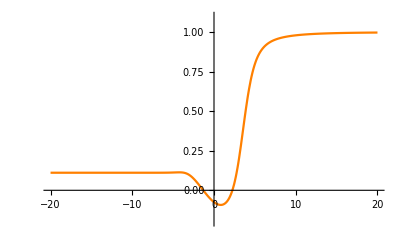

```mathematica
Kplot9=Plot[{avK9f[0.1,1.0,L]/9.0},{L,-20.0,20.0},PlotRange->{-0.2,1.1},PlotStyle->Orange]
```

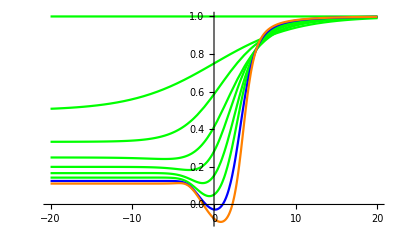

```mathematica
Show[Kplot1,Kplot2,Kplot3,Kplot4,Kplot5,Kplot6,Kplot7,Kplot8,Kplot9]
```

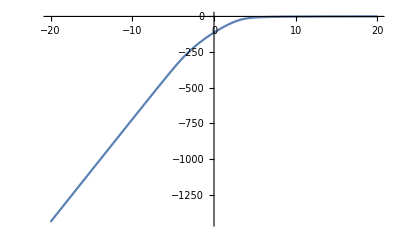

```mathematica
Fplot9=Plot[freeF9[0.1,1.0,L],{L,-20,20},PlotRange->All]
```

```mathematica
e9=Energies[g9u,H0Tot[1.0,-1.0],50];
```

Now computing energy of graph 22889

Now computing energy of graph 45778

Now computing energy of graph 68667

Now computing energy of graph 91556

Now computing energy of graph 114445

Now computing energy of graph 137334

Now computing energy of graph 160223

Now computing energy of graph 183112

Now computing energy of graph 206001

Now computing energy of graph 228890

Now computing energy of graph 251779

Now computing energy of graph 274668

```mathematica
e9[[20]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
GraphPlot3D[-Graphics-,ImageSize->Medium,EdgeRenderingFunction->({Cylinder[#1,0.03]}&),VertexRenderingFunction->({Sphere[#,0.06]}&)]
```

-Graphics3D-

```mathematica
AvgDim[Normal[AdjacencyMatrix[-Graphics-]]]
Dims[Normal[AdjacencyMatrix[-Graphics-]]]
Valencyvec[Normal[AdjacencyMatrix[-Graphics-]]]
```

3

{3,3,3,3,3,3,3,3,3}

{6,6,6,6,6,6,6,6,8}

```mathematica
Curvatures[Normal[AdjacencyMatrix[-Graphics-]]]
GCurvature[Normal[AdjacencyMatrix[-Graphics-]]]
```

{1/12,1/12,1/12,1/6,1/6,1/6,1/6,1/6,-1/12}

1

```mathematica
Map[AvgDim[#]&,Map[Normal,Map[AdjacencyMatrix,e9[[20]]]]]//N
```

{2.91667,3.18056,2.75,3.25,3.,3.,3.21667,3.,3.3619,3.55556,4.,3.73333,3.53333,3.52372,3.,3.38889,3.5,3.28095,3.23598,3.46667,3.30864,3.41808,3.35132}

```mathematica
Map[AvgDeg[#]&,Map[Normal,Map[AdjacencyMatrix,e9[[20]]]]]//N
```

{6.22222,6.22222,6.22222,6.22222,6.22222,6.22222,6.22222,6.22222,6.22222,6.22222,6.22222,6.22222,6.22222,6.22222,6.22222,6.22222,6.22222,6.22222,6.22222,6.22222,6.22222,6.22222,6.22222}

## N = 10

```mathematica
(*avdim10=ExpectationValue[g10u,AvgDim,H0Tot[J,L],b];
```

Working on energy of graph 100000

Working on energy of graph 200000

Working on energy of graph 300000

Working on energy of graph 400000

Working on energy of graph 500000

Working on energy of graph 600000

Working on energy of graph 700000

Working on energy of graph 800000

Working on energy of graph 900000

Working on energy of graph 1000000

Working on energy of graph 1100000

Working on energy of graph 1200000

Working on energy of graph 1300000

Working on energy of graph 1400000

Working on energy of graph 1500000

Working on energy of graph 1600000

Working on energy of graph 1700000

Working on energy of graph 1800000

Working on energy of graph 1900000

Working on energy of graph 2000000

Working on energy of graph 2100000

Working on energy of graph 2200000

Working on energy of graph 2300000

Working on energy of graph 2400000

Working on energy of graph 2500000

Working on energy of graph 2600000

Working on energy of graph 2700000

Working on energy of graph 2800000

Working on energy of graph 2900000

Working on energy of graph 3000000

Working on energy of graph 3100000

Working on energy of graph 3200000

Working on energy of graph 3300000

Working on energy of graph 3400000

Working on energy of graph 3500000

Working on energy of graph 3600000

Working on energy of graph 3700000

Working on energy of graph 3800000

Working on energy of graph 3900000

Working on energy of graph 4000000

Working on energy of graph 4100000

Working on energy of graph 4200000

Working on energy of graph 4300000

Working on energy of graph 4400000

Working on energy of graph 4500000

Working on energy of graph 4600000

Working on energy of graph 4700000

Working on energy of graph 4800000

Working on energy of graph 4900000

Working on energy of graph 5000000

Working on energy of graph 5100000

Working on energy of graph 5200000

Working on energy of graph 5300000

Working on energy of graph 5400000

Working on energy of graph 5500000

Working on energy of graph 5600000

Working on energy of graph 5700000

Working on energy of graph 5800000

Working on energy of graph 5900000

Working on energy of graph 6000000

Working on energy of graph 6100000

Working on energy of graph 6200000

Working on energy of graph 6300000

Working on energy of graph 6400000

Working on energy of graph 6500000

Working on energy of graph 6600000

Working on energy of graph 6700000

Working on energy of graph 6800000

Working on energy of graph 6900000

Working on energy of graph 7000000

Working on energy of graph 7100000

Working on energy of graph 7200000

Working on energy of graph 7300000

Working on energy of graph 7400000

Working on energy of graph 7500000

Working on energy of graph 7600000

Working on energy of graph 7700000

Working on energy of graph 7800000

Working on energy of graph 7900000

Working on energy of graph 8000000

Working on energy of graph 8100000

Working on energy of graph 8200000

Working on energy of graph 8300000

Working on energy of graph 8400000

Working on energy of graph 8500000

Working on energy of graph 8600000

Working on energy of graph 8700000

Working on energy of graph 8800000

Working on energy of graph 8900000

Working on energy of graph 9000000

Working on energy of graph 9100000

Working on energy of graph 9200000

Working on energy of graph 9300000

Working on energy of graph 9400000

Working on energy of graph 9500000

Working on energy of graph 9600000

Working on energy of graph 9700000

Working on energy of graph 9800000

Working on energy of graph 9900000

Working on energy of graph 10000000

Working on energy of graph 10100000

Working on energy of graph 10200000

Working on energy of graph 10300000

Working on energy of graph 10400000

Working on energy of graph 10500000

Working on energy of graph 10600000

Working on energy of graph 10700000

Working on energy of graph 10800000

Working on energy of graph 10900000

Working on energy of graph 11000000

Working on energy of graph 11100000

Working on energy of graph 11200000

Working on energy of graph 11300000

Working on energy of graph 11400000

Working on energy of graph 11500000

Working on energy of graph 11600000

Working on energy of graph 11700000

Working on energy of graph 11800000

Working on energy of graph 11900000

Working on energy of graph 12000000

Working on function value of graph = 100000

Working on function value of graph = 200000

Working on function value of graph = 300000

Working on function value of graph = 400000

Working on function value of graph = 500000

Working on function value of graph = 600000

Working on function value of graph = 700000

Working on function value of graph = 800000

Working on function value of graph = 900000

Working on function value of graph = 1000000

Working on function value of graph = 1100000

Working on function value of graph = 1200000

Working on function value of graph = 1300000

Working on function value of graph = 1400000

Working on function value of graph = 1500000

Working on function value of graph = 1600000

Working on function value of graph = 1700000

Working on function value of graph = 1800000

Working on function value of graph = 1900000

Working on function value of graph = 2000000

Working on function value of graph = 2100000

Working on function value of graph = 2200000

Working on function value of graph = 2300000

Working on function value of graph = 2400000

Working on function value of graph = 2500000

Working on function value of graph = 2600000

Working on function value of graph = 2700000

Working on function value of graph = 2800000

Working on function value of graph = 2900000

Working on function value of graph = 3000000

Working on function value of graph = 3100000

Working on function value of graph = 3200000

Working on function value of graph = 3300000

Working on function value of graph = 3400000

Working on function value of graph = 3500000

Working on function value of graph = 3600000

Working on function value of graph = 3700000

Working on function value of graph = 3800000

Working on function value of graph = 3900000

Working on function value of graph = 4000000

Working on function value of graph = 4100000

Working on function value of graph = 4200000

Working on function value of graph = 4300000

Working on function value of graph = 4400000

Working on function value of graph = 4500000

Working on function value of graph = 4600000

Working on function value of graph = 4700000

Working on function value of graph = 4800000

Working on function value of graph = 4900000

Working on function value of graph = 5000000

Working on function value of graph = 5100000

Working on function value of graph = 5200000

Working on function value of graph = 5300000

Working on function value of graph = 5400000

Working on function value of graph = 5500000

Working on function value of graph = 5600000

Working on function value of graph = 5700000

Working on function value of graph = 5800000

Working on function value of graph = 5900000

Working on function value of graph = 6000000

Working on function value of graph = 6100000

Working on function value of graph = 6200000

Working on function value of graph = 6300000

Working on function value of graph = 6400000

Working on function value of graph = 6500000

Working on function value of graph = 6600000

Working on function value of graph = 6700000

Working on function value of graph = 6800000

Working on function value of graph = 6900000

Working on function value of graph = 7000000

Working on function value of graph = 7100000

Working on function value of graph = 7200000

Working on function value of graph = 7300000

Working on function value of graph = 7400000

Working on function value of graph = 7500000

Working on function value of graph = 7600000

Working on function value of graph = 7700000

Working on function value of graph = 7800000

Working on function value of graph = 7900000

Working on function value of graph = 8000000

Working on function value of graph = 8100000

Working on function value of graph = 8200000

Working on function value of graph = 8300000

Working on function value of graph = 8400000

Working on function value of graph = 8500000

Working on function value of graph = 8600000

Working on function value of graph = 8700000

Working on function value of graph = 8800000

Working on function value of graph = 8900000

Working on function value of graph = 9000000

Working on function value of graph = 9100000

Working on function value of graph = 9200000

Working on function value of graph = 9300000

Working on function value of graph = 9400000

Working on function value of graph = 9500000

Working on function value of graph = 9600000

Working on function value of graph = 9700000

Working on function value of graph = 9800000

Working on function value of graph = 9900000

Working on function value of graph = 10000000

Working on function value of graph = 10100000

Working on function value of graph = 10200000

Working on function value of graph = 10300000

Working on function value of graph = 10400000

Working on function value of graph = 10500000

Working on function value of graph = 10600000

Working on function value of graph = 10700000

Working on function value of graph = 10800000

Working on function value of graph = 10900000

Working on function value of graph = 11000000

Working on function value of graph = 11100000

Working on function value of graph = 11200000

Working on function value of graph = 11300000

Working on function value of graph = 11400000

Working on function value of graph = 11500000

Working on function value of graph = 11600000

Working on function value of graph = 11700000

Working on function value of graph = 11800000

Working on function value of graph = 11900000

Working on function value of graph = 12000000

```mathematica
(*avdeg10=ExpectationValue[g10u,AvgDeg,H0Tot[J,L],b];
```

```mathematica
(*avK10=ExpectationValue[g10u,EulerChi,H0Tot[J,L],b];
```

Working on energy of graph 100000

Working on energy of graph 200000

Working on energy of graph 300000

Working on energy of graph 400000

Working on energy of graph 500000

Working on energy of graph 600000

Working on energy of graph 700000

Working on energy of graph 800000

Working on energy of graph 900000

Working on energy of graph 1000000

Working on energy of graph 1100000

Working on energy of graph 1200000

Working on energy of graph 1300000

Working on energy of graph 1400000

Working on energy of graph 1500000

Working on energy of graph 1600000

Working on energy of graph 1700000

Working on energy of graph 1800000

Working on energy of graph 1900000

Working on energy of graph 2000000

Working on energy of graph 2100000

Working on energy of graph 2200000

Working on energy of graph 2300000

Working on energy of graph 2400000

Working on energy of graph 2500000

Working on energy of graph 2600000

Working on energy of graph 2700000

Working on energy of graph 2800000

Working on energy of graph 2900000

Working on energy of graph 3000000

Working on energy of graph 3100000

Working on energy of graph 3200000

Working on energy of graph 3300000

Working on energy of graph 3400000

Working on energy of graph 3500000

Working on energy of graph 3600000

Working on energy of graph 3700000

Working on energy of graph 3800000

Working on energy of graph 3900000

Working on energy of graph 4000000

Working on energy of graph 4100000

Working on energy of graph 4200000

Working on energy of graph 4300000

Working on energy of graph 4400000

Working on energy of graph 4500000

Working on energy of graph 4600000

Working on energy of graph 4700000

Working on energy of graph 4800000

Working on energy of graph 4900000

Working on energy of graph 5000000

Working on energy of graph 5100000

Working on energy of graph 5200000

Working on energy of graph 5300000

Working on energy of graph 5400000

Working on energy of graph 5500000

Working on energy of graph 5600000

Working on energy of graph 5700000

Working on energy of graph 5800000

Working on energy of graph 5900000

Working on energy of graph 6000000

Working on energy of graph 6100000

Working on energy of graph 6200000

Working on energy of graph 6300000

Working on energy of graph 6400000

Working on energy of graph 6500000

Working on energy of graph 6600000

Working on energy of graph 6700000

Working on energy of graph 6800000

Working on energy of graph 6900000

Working on energy of graph 7000000

Working on energy of graph 7100000

Working on energy of graph 7200000

Working on energy of graph 7300000

Working on energy of graph 7400000

Working on energy of graph 7500000

Working on energy of graph 7600000

Working on energy of graph 7700000

Working on energy of graph 7800000

Working on energy of graph 7900000

Working on energy of graph 8000000

Working on energy of graph 8100000

Working on energy of graph 8200000

Working on energy of graph 8300000

Working on energy of graph 8400000

Working on energy of graph 8500000

Working on energy of graph 8600000

Working on energy of graph 8700000

Working on energy of graph 8800000

Working on energy of graph 8900000

Working on energy of graph 9000000

Working on energy of graph 9100000

Working on energy of graph 9200000

Working on energy of graph 9300000

Working on energy of graph 9400000

Working on energy of graph 9500000

Working on energy of graph 9600000

Working on energy of graph 9700000

Working on energy of graph 9800000

Working on energy of graph 9900000

Working on energy of graph 10000000

Working on energy of graph 10100000

Working on energy of graph 10200000

Working on energy of graph 10300000

Working on energy of graph 10400000

Working on energy of graph 10500000

Working on energy of graph 10600000

Working on energy of graph 10700000

Working on energy of graph 10800000

Working on energy of graph 10900000

Working on energy of graph 11000000

Working on energy of graph 11100000

Working on energy of graph 11200000

Working on energy of graph 11300000

Working on energy of graph 11400000

Working on energy of graph 11500000

Working on energy of graph 11600000

Working on energy of graph 11700000

Working on energy of graph 11800000

Working on energy of graph 11900000

Working on energy of graph 12000000

Working on function value of graph = 100000

Working on function value of graph = 200000

Working on function value of graph = 300000

Working on function value of graph = 400000

Working on function value of graph = 500000

Working on function value of graph = 600000

Working on function value of graph = 700000

Working on function value of graph = 800000

Working on function value of graph = 900000

Working on function value of graph = 1000000

Working on function value of graph = 1100000

Working on function value of graph = 1200000

Working on function value of graph = 1300000

Working on function value of graph = 1400000

Working on function value of graph = 1500000

Working on function value of graph = 1600000

Working on function value of graph = 1700000

Working on function value of graph = 1800000

Working on function value of graph = 1900000

Working on function value of graph = 2000000

Working on function value of graph = 2100000

Working on function value of graph = 2200000

Working on function value of graph = 2300000

Working on function value of graph = 2400000

Working on function value of graph = 2500000

Working on function value of graph = 2600000

Working on function value of graph = 2700000

Working on function value of graph = 2800000

Working on function value of graph = 2900000

Working on function value of graph = 3000000

Working on function value of graph = 3100000

Working on function value of graph = 3200000

Working on function value of graph = 3300000

Working on function value of graph = 3400000

Working on function value of graph = 3500000

Working on function value of graph = 3600000

Working on function value of graph = 3700000

Working on function value of graph = 3800000

Working on function value of graph = 3900000

Working on function value of graph = 4000000

Working on function value of graph = 4100000

Working on function value of graph = 4200000

Working on function value of graph = 4300000

Working on function value of graph = 4400000

Working on function value of graph = 4500000

Working on function value of graph = 4600000

Working on function value of graph = 4700000

Working on function value of graph = 4800000

Working on function value of graph = 4900000

Working on function value of graph = 5000000

Working on function value of graph = 5100000

Working on function value of graph = 5200000

Working on function value of graph = 5300000

Working on function value of graph = 5400000

Working on function value of graph = 5500000

Working on function value of graph = 5600000

Working on function value of graph = 5700000

Working on function value of graph = 5800000

Working on function value of graph = 5900000

Working on function value of graph = 6000000

Working on function value of graph = 6100000

Working on function value of graph = 6200000

Working on function value of graph = 6300000

Working on function value of graph = 6400000

Working on function value of graph = 6500000

Working on function value of graph = 6600000

Working on function value of graph = 6700000

Working on function value of graph = 6800000

Working on function value of graph = 6900000

Working on function value of graph = 7000000

Working on function value of graph = 7100000

Working on function value of graph = 7200000

Working on function value of graph = 7300000

Working on function value of graph = 7400000

Working on function value of graph = 7500000

Working on function value of graph = 7600000

Working on function value of graph = 7700000

Working on function value of graph = 7800000

Working on function value of graph = 7900000

Working on function value of graph = 8000000

Working on function value of graph = 8100000

Working on function value of graph = 8200000

Working on function value of graph = 8300000

Working on function value of graph = 8400000

Working on function value of graph = 8500000

Working on function value of graph = 8600000

Working on function value of graph = 8700000

Working on function value of graph = 8800000

Working on function value of graph = 8900000

Working on function value of graph = 9000000

Working on function value of graph = 9100000

Working on function value of graph = 9200000

Working on function value of graph = 9300000

Working on function value of graph = 9400000

Working on function value of graph = 9500000

Working on function value of graph = 9600000

Working on function value of graph = 9700000

Working on function value of graph = 9800000

Working on function value of graph = 9900000

Working on function value of graph = 10000000

Working on function value of graph = 10100000

Working on function value of graph = 10200000

Working on function value of graph = 10300000

Working on function value of graph = 10400000

Working on function value of graph = 10500000

Working on function value of graph = 10600000

Working on function value of graph = 10700000

Working on function value of graph = 10800000

Working on function value of graph = 10900000

Working on function value of graph = 11000000

Working on function value of graph = 11100000

Working on function value of graph = 11200000

Working on function value of graph = 11300000

Working on function value of graph = 11400000

Working on function value of graph = 11500000

Working on function value of graph = 11600000

Working on function value of graph = 11700000

Working on function value of graph = 11800000

Working on function value of graph = 11900000

Working on function value of graph = 12000000

```mathematica
(*avdim10f[b_,J_,L_]=avdim10[[3]];*)
```

```mathematica
(*avdeg10f[b_,J_,L_]=avdeg10[[3]];
```

```mathematica
(*freeF10[b_,J_,L_]=avdeg10[[2]];
```

```mathematica
(*avK10f[b_,J_,L_]=avK10[[3]];
```

```mathematica
Magnetizationd10[b_,J_,L_]=D[freeF10[b,J,L],{L,1}]/10.0;
Chideg10[b_,J_,L_]=-D[Magnetizationd10[b,J,L],{L,1}]/(10.0*b);
```

```mathematica
delD10[b_,J_,L_]=D[freeF10[b,J,L],{J,1}]/10.0;(*the expectation value of the square of the total degree difference within a graph*)
```

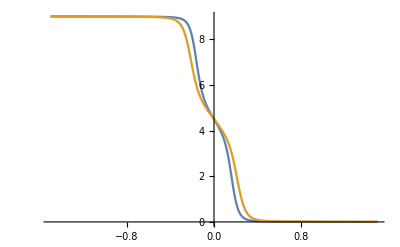

```mathematica
Plot[{Magnetizationd10[1.2,1.0,L],avdeg10f[1.0,1.0,L]},{L,-1.5,1.5},PlotRange->All]
```

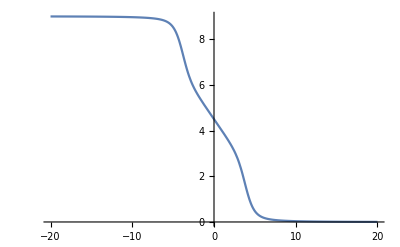

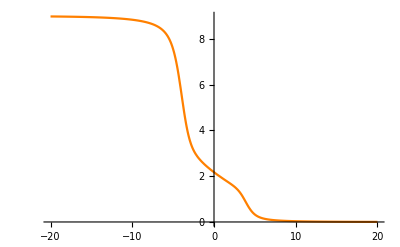

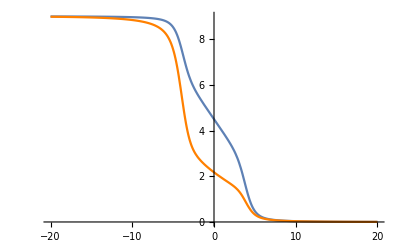

```mathematica
degplot10=Plot[avdeg10f[0.1,1.0,L],{L,-20,20},PlotRange->All]
dimplot10=Plot[avdim10f[0.1,1.0,L],{L,-20.0,20.0},PlotRange->All,PlotStyle->Orange]
Show[degplot10,dimplot10]
```

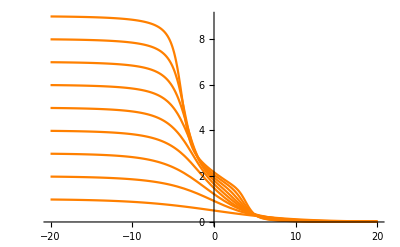

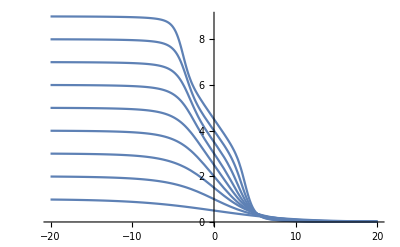

```mathematica
Show[dimplot2,dimplot3,dimplot4,dimplot5,dimplot6,dimplot7,dimplot8,dimplot9,dimplot10]
Show[degplot2,degplot3,degplot4,degplot5,degplot6,degplot7,degplot8,degplot9,degplot10]
```

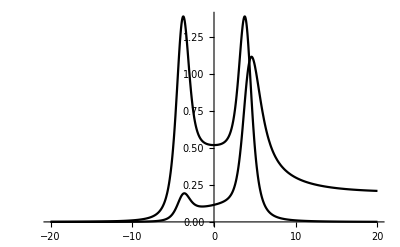

```mathematica
chidegplot10=Plot[{Chideg10[0.1,1.0,L],Chideg10[0.1,1.0,L]/avdeg10f[0.1,1.0,L]},{L,-20.0,20.0},PlotRange->All,PlotStyle->Black]
```

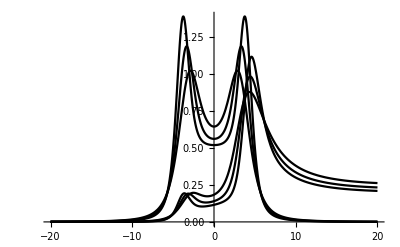

```mathematica
Show[chidegplot8,chidegplot9,chidegplot10]
```

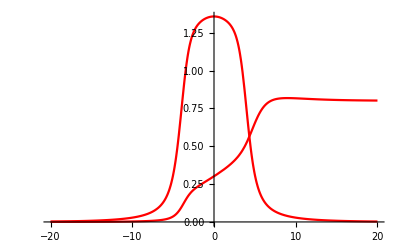

```mathematica
deldplot10=Plot[{delD10[0.1,1.0,L],delD10[0.1,1.0,L]/avdeg10f[0.1,1.0,L]},{L,-20.0,20.0},PlotRange->All,PlotStyle->Red]
```

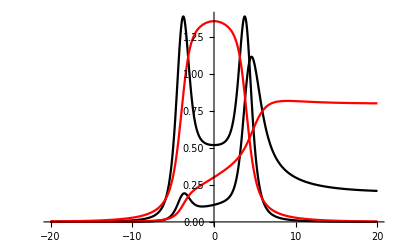

```mathematica
Show[chidegplot10,deldplot10]
```

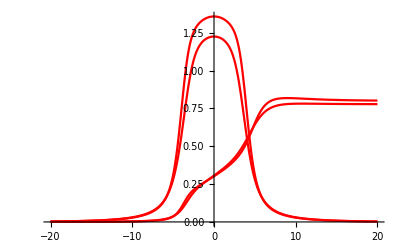

```mathematica
Show[deldplot9,deldplot10]
```

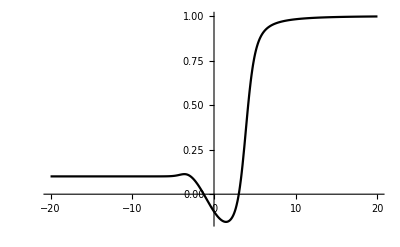

```mathematica
Kplot10=Plot[{avK10f[0.1,1.0,L]/10.0},{L,-20.0,20.0},PlotRange->All,PlotStyle->Black]
```

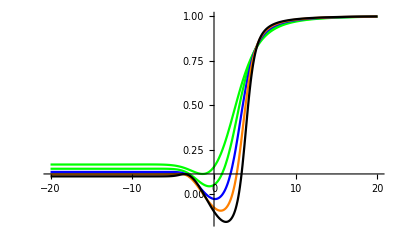

```mathematica
Show[Kplot6,Kplot7,Kplot8,Kplot9,Kplot10]
```

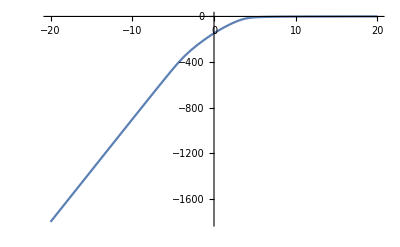

```mathematica
Fplot10=Plot[freeF10[0.1,1.0,L],{L,-20,20},PlotRange->All]
```

```mathematica
e10=Energies[g10u,H0Tot[1.0,-1.0],60];
```

Now computing energy of graph 100000

Now computing energy of graph 200000

Now computing energy of graph 300000

Now computing energy of graph 400000

Now computing energy of graph 500000

Now computing energy of graph 600000

Now computing energy of graph 700000

Now computing energy of graph 800000

Now computing energy of graph 900000

Now computing energy of graph 1000000

Now computing energy of graph 1100000

Now computing energy of graph 1200000

Now computing energy of graph 1300000

Now computing energy of graph 1400000

Now computing energy of graph 1500000

Now computing energy of graph 1600000

Now computing energy of graph 1700000

Now computing energy of graph 1800000

Now computing energy of graph 1900000

Now computing energy of graph 2000000

Now computing energy of graph 2100000

Now computing energy of graph 2200000

Now computing energy of graph 2300000

Now computing energy of graph 2400000

Now computing energy of graph 2500000

Now computing energy of graph 2600000

Now computing energy of graph 2700000

Now computing energy of graph 2800000

Now computing energy of graph 2900000

Now computing energy of graph 3000000

Now computing energy of graph 3100000

Now computing energy of graph 3200000

Now computing energy of graph 3300000

Now computing energy of graph 3400000

Now computing energy of graph 3500000

Now computing energy of graph 3600000

Now computing energy of graph 3700000

Now computing energy of graph 3800000

Now computing energy of graph 3900000

Now computing energy of graph 4000000

Now computing energy of graph 4100000

Now computing energy of graph 4200000

Now computing energy of graph 4300000

Now computing energy of graph 4400000

Now computing energy of graph 4500000

Now computing energy of graph 4600000

Now computing energy of graph 4700000

Now computing energy of graph 4800000

Now computing energy of graph 4900000

Now computing energy of graph 5000000

Now computing energy of graph 5100000

Now computing energy of graph 5200000

Now computing energy of graph 5300000

Now computing energy of graph 5400000

Now computing energy of graph 5500000

Now computing energy of graph 5600000

Now computing energy of graph 5700000

Now computing energy of graph 5800000

Now computing energy of graph 5900000

Now computing energy of graph 6000000

Now computing energy of graph 6100000

Now computing energy of graph 6200000

Now computing energy of graph 6300000

Now computing energy of graph 6400000

Now computing energy of graph 6500000

Now computing energy of graph 6600000

Now computing energy of graph 6700000

Now computing energy of graph 6800000

Now computing energy of graph 6900000

Now computing energy of graph 7000000

Now computing energy of graph 7100000

Now computing energy of graph 7200000

Now computing energy of graph 7300000

Now computing energy of graph 7400000

Now computing energy of graph 7500000

Now computing energy of graph 7600000

Now computing energy of graph 7700000

Now computing energy of graph 7800000

Now computing energy of graph 7900000

Now computing energy of graph 8000000

Now computing energy of graph 8100000

Now computing energy of graph 8200000

Now computing energy of graph 8300000

Now computing energy of graph 8400000

Now computing energy of graph 8500000

Now computing energy of graph 8600000

Now computing energy of graph 8700000

Now computing energy of graph 8800000

Now computing energy of graph 8900000

Now computing energy of graph 9000000

Now computing energy of graph 9100000

Now computing energy of graph 9200000

Now computing energy of graph 9300000

Now computing energy of graph 9400000

Now computing energy of graph 9500000

Now computing energy of graph 9600000

Now computing energy of graph 9700000

Now computing energy of graph 9800000

Now computing energy of graph 9900000

Now computing energy of graph 10000000

Now computing energy of graph 10100000

Now computing energy of graph 10200000

Now computing energy of graph 10300000

Now computing energy of graph 10400000

Now computing energy of graph 10500000

Now computing energy of graph 10600000

Now computing energy of graph 10700000

Now computing energy of graph 10800000

Now computing energy of graph 10900000

Now computing energy of graph 11000000

Now computing energy of graph 11100000

Now computing energy of graph 11200000

Now computing energy of graph 11300000

Now computing energy of graph 11400000

Now computing energy of graph 11500000

Now computing energy of graph 11600000

Now computing energy of graph 11700000

Now computing energy of graph 11800000

Now computing energy of graph 11900000

Now computing energy of graph 12000000

```mathematica
GraphPlot3D[-Graphics-,ImageSize->Medium,EdgeRenderingFunction->({Cylinder[#1,0.03]}&),VertexRenderingFunction->({Sphere[#,0.06]}&)]
```

-Graphics3D-

```mathematica
AvgDim[Normal[AdjacencyMatrix[-Graphics-]]]//N
Dims[Normal[AdjacencyMatrix[-Graphics-]]]//N
Valencyvec[Normal[AdjacencyMatrix[-Graphics-]]]//N
```

2.4

{3.,2.,2.,2.,3.,2.4,2.4,2.4,2.4,2.4}

{6.,5.,5.,5.,6.,6.,6.,6.,6.,7.}

```mathematica
Curvatures[Normal[AdjacencyMatrix[-Graphics-]]]
GCurvature[Normal[AdjacencyMatrix[-Graphics-]]]
```

{-1/12,-1/2,-1/2,-1/2,-1/12,-1/4,-1/4,-1/4,-1/4,2/3}

-2

```mathematica
Map[AvgDim[#]&,Map[Normal,Map[AdjacencyMatrix,e10[[2]]]]]//N
```

{8.}

```mathematica
Map[AvgDeg[#]&,Map[Normal,Map[AdjacencyMatrix,e10[[2]]]]]//N
```

{8.8}

```mathematica
Map[AvgDim[#]&,Map[Normal,Map[AdjacencyMatrix,e10[[10]]]]]//N
Map[AvgDeg[#]&,Map[Normal,Map[AdjacencyMatrix,e10[[10]]]]]//N
```

{7.}

{8.4}

```mathematica
Map[AvgDim[#]&,Map[Normal,Map[AdjacencyMatrix,e10[[60]]]]]//N
Map[AvgDeg[#]&,Map[Normal,Map[AdjacencyMatrix,e10[[60]]]]]//N
```

{4.54286,5.,4.91667,4.58333,4.56944,4.70952,4.97619,4.38889,4.54861,4.94444,4.91667,4.90476,5.02381,5.07639,5.08333,4.78571,4.77381,4.975,4.65714,4.78264,4.61429,4.72619,4.78646,4.77222,4.64286,5.,5.19524,5.1619,5.19375,5.,4.78095,4.90476,5.,4.81389,4.77381,5.125,5.12708,5.20208,5.03466,4.81587,5.03333,5.21693,4.53333,4.65833,4.53819,4.57143,5.07153,4.77361,5.06261,5.21481,5.0375,5.1,5.09375,4.81771,4.65,5.45714,5.,5.32381,5.28571,5.28125,5.29167,5.35556,5.25417,5.16349,5.25714,5.21667,5.23167,5.75,5.1875}

{7.2,7.2,7.2,7.2,7.2,7.2,7.2,7.2,7.2,7.2,7.2,7.2,7.2,7.2,7.2,7.2,7.2,7.2,7.2,7.2,7.2,7.2,7.2,7.2,7.2,7.2,7.2,7.2,7.2,7.2,7.2,7.2,7.2,7.2,7.2,7.2,7.2,7.2,7.2,7.2,7.2,7.2,7.2,7.2,7.2,7.2,7.2,7.2,7.2,7.2,7.2,7.2,7.2,7.2,7.2,7.2,7.2,7.2,7.2,7.2,7.2,7.2,7.2,7.2,7.2,7.2,7.2,7.2,7.2}

## N = 10, Only Eulerian graphs

```mathematica
avdim10eul=ExpectationValue[eul10,AvgDim,H0Tot[J,L],b];
```

```mathematica
avdeg10eul=ExpectationValue[eul10,AvgDeg,H0Tot[J,L],b];
```

```mathematica
avK10eul=ExpectationValue[eul10,Curvature,H0Tot[J,L],b];
```

```mathematica
avdim10eulf[b_,J_,L_]=avdim10eul[[3]];
```

```mathematica
avdeg10eulf[b_,J_,L_]=avdeg10eul[[3]];
```

```mathematica
freeF10eul[b_,J_,L_]=avdeg10eul[[2]];
```

```mathematica
avK10eulf[b_,J_,L_]=avK10eul[[3]];
```

```mathematica
Magnetizationd10eul[b_,J_,L_]=D[freeF10eul[b,J,L],{L,1}]/10.0;
Chideg10eul[b_,J_,L_]=-D[Magnetizationd10eul[b,J,L],{L,1}]/(10.0*b);
```

```mathematica
delD10eul[b_,J_,L_]=D[freeF10eul[b,J,L],{J,1}]/10.0;(*the expectation value of the square of the total degree difference within a graph*)
```

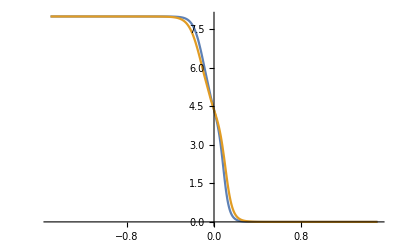

```mathematica
Plot[{Magnetizationd10eul[1.2,1.0,L],avdeg10eulf[1.0,1.0,L]},{L,-1.5,1.5},PlotRange->All]
```

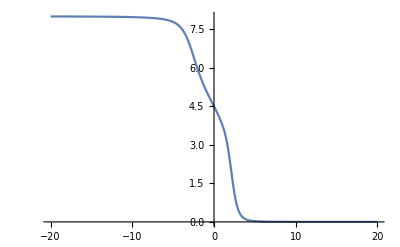

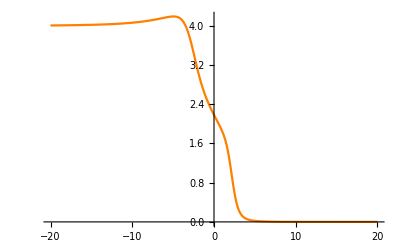

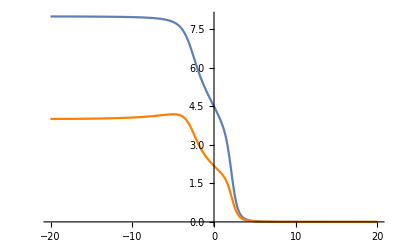

```mathematica
degplot10eul=Plot[avdeg10eulf[0.1,1.0,L],{L,-20,20},PlotRange->All]
dimplot10eul=Plot[avdim10eulf[0.1,1.0,L],{L,-20.0,20.0},PlotRange->All,PlotStyle->Orange]
Show[degplot10eul,dimplot10eul]
```

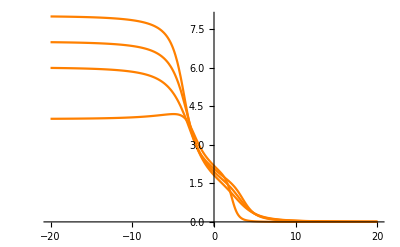

```mathematica
Show[dimplot7,dimplot8,dimplot9,dimplot10eul]
```

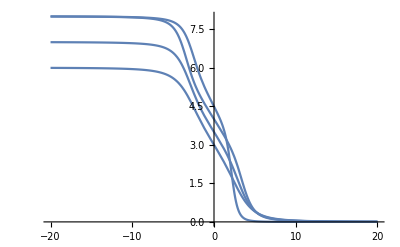

```mathematica
Show[degplot7,degplot8,degplot9,degplot10eul]
```

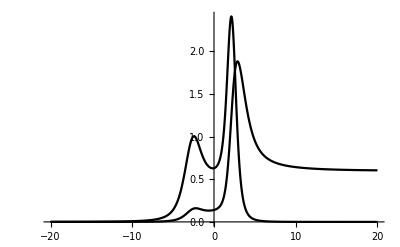

```mathematica
chidegplot10eul=Plot[{Chideg10eul[0.1,1.0,L],Chideg10eul[0.1,1.0,L]/avdeg10eulf[0.1,1.0,L]},{L,-20.0,20.0},PlotRange->All,PlotStyle->Black]
```

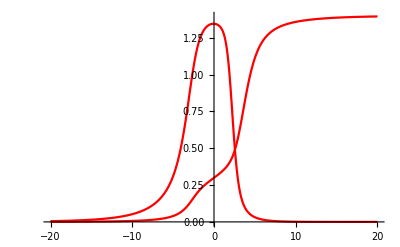

```mathematica
deldplot10eul=Plot[{delD10eul[0.1,1.0,L],delD10eul[0.1,1.0,L]/avdeg10eulf[0.1,1.0,L]},{L,-20.0,20.0},PlotRange->All,PlotStyle->Red]
```

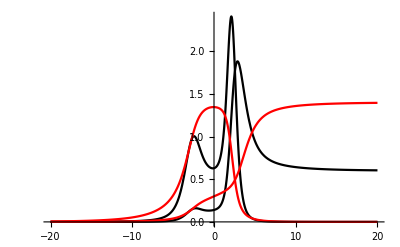

```mathematica
Show[chidegplot10eul,deldplot10eul]
```

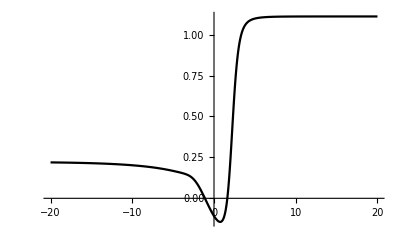

```mathematica
Kplot10eul=Plot[{avK10eulf[0.1,1.0,L]/9.0},{L,-20.0,20.0},PlotRange->All,PlotStyle->Black]
```

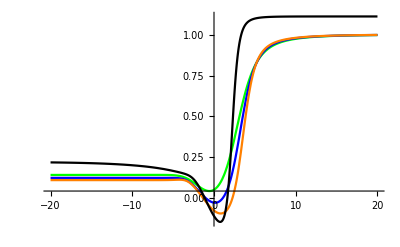

```mathematica
Show[Kplot7,Kplot8,Kplot9,Kplot10eul]
```

```mathematica
EulerChi[Table[Table[0,{9}],{9}]]
Curvatures[Table[Table[0,{9}],{9}]]
```

9

{1,1,1,1,1,1,1,1,1}

```mathematica
EulerChi[MakeKn[9]]
```

1

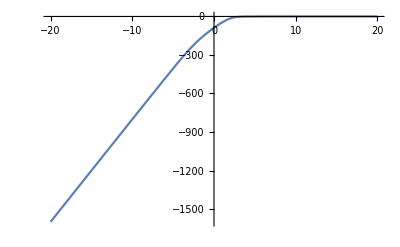

```mathematica
Fplot10eul=Plot[freeF10eul[0.1,1.0,L],{L,-20,20},PlotRange->All]
```

```mathematica
Energies[eul10,H0Tot[1.0,-1.0],5]
```

Now computing energy of graph 1656

Now computing energy of graph 3312

Now computing energy of graph 4968

Now computing energy of graph 6624

Now computing energy of graph 8280

Now computing energy of graph 9936

Now computing energy of graph 11592

Now computing energy of graph 13248

Now computing energy of graph 14904

Now computing energy of graph 16560

Now computing energy of graph 18216

Now computing energy of graph 19872

Now computing energy of graph 21528

Now computing energy of graph 23184

Now computing energy of graph 24840

Now computing energy of graph 26496

Now computing energy of graph 28152

Now computing energy of graph 29808

Now computing energy of graph 31464

Now computing energy of graph 33120

<|-80.→{-Graphics-},-74.4→{-Graphics-},-69.6→{-Graphics-,-Graphics-},-65.6→{-Graphics-,-Graphics-,-Graphics-},-62.4→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}|>

```mathematica
AllDims[Normal[AdjacencyMatrix[-Graphics-]]]//N
Valencyvec[Normal[AdjacencyMatrix[-Graphics-]]]
```

{3.,3.,3.,3.,3.,3.,3.,3.,3.,3.}

{6,6,6,6,8,8,8,8,8,8}

```mathematica
GraphPlot3D[-Graphics-]
```

-Graphics3D-

HEuler

## N = 6

```mathematica
avdim6=ExpectationValue[g6u,AvgDim,HEulerWS[J,L],b];
avdeg6=ExpectationValue[g6u,AvgDeg,HEulerWS[J,L],b];
avK6=ExpectationValue[g6u,EulerChi,HEulerWS[J,L],b];
avdim6f[b_,J_,L_]=avdim6[[3]];
avdeg6f[b_,J_,L_]=avdeg6[[3]];
freeF6[b_,J_,L_]=avdeg6[[2]];
avK6f[b_,J_,L_]=avK6[[3]];
Magnetizationd6[b_,J_,L_]=D[freeF6[b,J,L],{L,1}]/6.0;
Chideg6[b_,J_,L_]=-D[Magnetizationd6[b,J,L],{L,1}]/(6.0*b);
delD6[b_,J_,L_]=ExpectationValue[g6u,H0[1.0],HEulerWS[J,L],b]/6.0;(*the expectation value of the square of the total degree difference within a graph*)
```

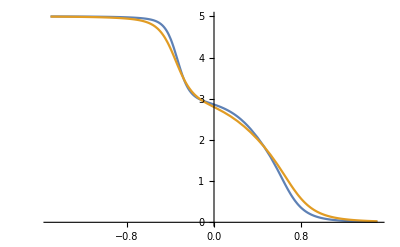

```mathematica
Plot[{Magnetizationd6[1.8,1.0,L],avdeg6f[1.4,1.0,L]},{L,-1.5,1.5},PlotRange->All]
```

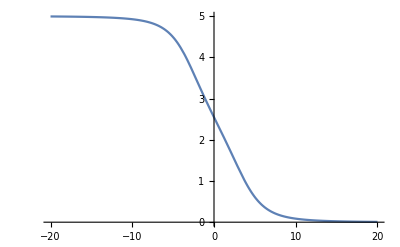

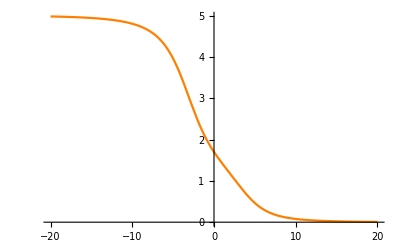

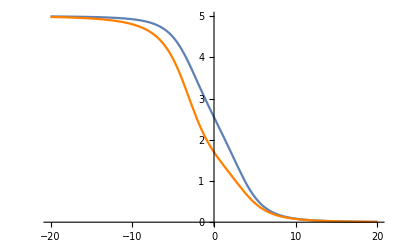

```mathematica
degplot6=Plot[avdeg6f[0.1,1.0,L],{L,-20,20},PlotRange->All]
dimplot6=Plot[avdim6f[0.1,1.0,L],{L,-20.0,20.0},PlotRange->All,PlotStyle->Orange]
Show[degplot6,dimplot6]
```

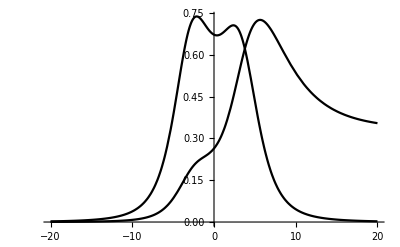

```mathematica
chidegplot6=Plot[{Chideg6[0.1,1.0,L],Chideg6[0.1,1.0,L]/avdeg6f[0.1,1.0,L]},{L,-20.0,20.0},PlotRange->All,PlotStyle->Black]
```

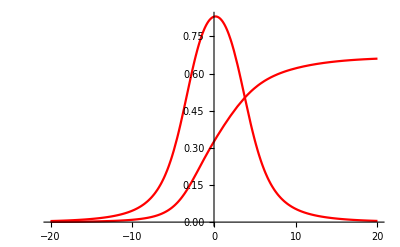

```mathematica
deldplot6=Plot[{delD6[0.1,1.0,L][[3]],delD6[0.1,1.0,L][[3]]/avdeg6f[0.1,1.0,L]},{L,-20.0,20.0},PlotRange->All,PlotStyle->Red]
```

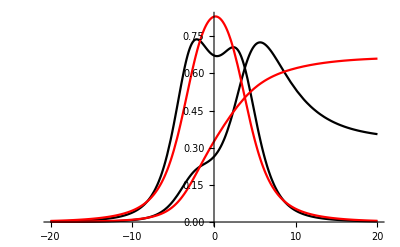

```mathematica
Show[chidegplot6,deldplot6]
```

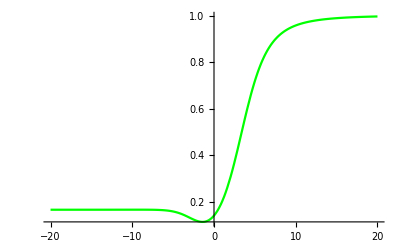

```mathematica
Kplot6=Plot[{avK6f[0.1,1.0,L]/6.0},{L,-20.0,20.0},PlotRange->All,PlotStyle->Green]
```

```mathematica
Show[Kplot1,Kplot2,Kplot3,Kplot4,Kplot5,Kplot6]
```

-Graphics-

```mathematica
Fplot6=Plot[freeF6[0.1,1.0,L],{L,-20,20},PlotRange->All]
```

-Graphics-

```mathematica
Energies[g6u,HEulerWS[1.0,-0.5],8]
```

<|-14.→{-Graphics-},-13.→{-Graphics-},-12.→{-Graphics-,-Graphics-,-Graphics-},-11.→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},-10.→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},-9.→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},-8.→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},-7.→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}|>

```mathematica
GraphPlot3D[-Graphics-,ImageSize->Medium,EdgeRenderingFunction->({Cylinder[#1,0.03]}&),VertexRenderingFunction->({Sphere[#,0.06]}&)]
```

-Graphics3D-

```mathematica
Dims[Normal[AdjacencyMatrix[-Graphics-]]]
AvgDim[Normal[AdjacencyMatrix[-Graphics-]]]
Valencyvec[Normal[AdjacencyMatrix[-Graphics-]]]
```

{2,2,2,2,2,2}

2

{4,4,4,4,4,4}

```mathematica
Curvatures[Normal[AdjacencyMatrix[-Graphics-]]]
GCurvature[Normal[AdjacencyMatrix[-Graphics-]]]
```

{1/3,1/3,1/3,1/3,1/3,1/3}

2

## N = 7

```mathematica
avdim7=ExpectationValue[g7u,AvgDim,HEulerWS[J,L],b];
```

```mathematica
avdeg7=ExpectationValue[g7u,AvgDeg,HEulerWS[J,L],b];
```

```mathematica
avK7=ExpectationValue[g7u,EulerChi,HEulerWS[J,L],b];
```

```mathematica
avdim7f[b_,J_,L_]=avdim7[[3]];
avdeg7f[b_,J_,L_]=avdeg7[[3]];
freeF7[b_,J_,L_]=avdeg7[[2]];
avK7f[b_,J_,L_]=avK7[[3]];
Magnetizationd7[b_,J_,L_]=D[freeF7[b,J,L],{L,1}]/7.0;
Chideg7[b_,J_,L_]=-D[Magnetizationd7[b,J,L],{L,1}]/(7.0*b);
delD7[b_,J_,L_]=ExpectationValue[g7u,H0[1.0],HEulerWS[J,L],b][[3]]/7.0;(*the expectation value of the square of the total degree difference within a graph*)
```

```mathematica
ExpectationValue[g7u,H0[1.0],HEulerWS[1.0,1.0],0.1]
```

{139.6,-49.3878,7.63028}

```mathematica
Plot[{Magnetizationd7[1.2,1.0,L],avdeg7f[1.6,1.0,L]},{L,-1.5,1.5},PlotRange->All]
```

-Graphics-

```mathematica
degplot7=Plot[avdeg7f[0.1,1.0,L],{L,-20,20},PlotRange->All]
dimplot7=Plot[avdim7f[0.1,1.0,L],{L,-20.0,20.0},PlotRange->All,PlotStyle->Orange]
Show[degplot7,dimplot7]
```

-Graphics-

-Graphics-

-Graphics-

```mathematica
chidegplot7=Plot[{Chideg7[0.1,1.0,L],Chideg7[0.1,1.0,L]/avdeg7f[0.1,1.0,L]},{L,-20.0,20.0},PlotRange->All,PlotStyle->Black]
```

-Graphics-

```mathematica
deldplot7=Plot[{delD7[0.1,1.0,L],delD7[0.1,1.0,L]/avdeg7f[0.1,1.0,L]},{L,-20.0,20.0},PlotRange->All,PlotStyle->Red]
```

-Graphics-

```mathematica
Show[chidegplot7,deldplot7]
```

-Graphics-

```mathematica
Kplot7=Plot[{avK7f[0.1,1.0,L]/7.0},{L,-20.0,20.0},PlotRange->All,PlotStyle->Green]
```

-Graphics-

```mathematica
Show[Kplot6,Kplot7]
```

-Graphics-

```mathematica
Fplot7=Plot[freeF7[0.1,1.0,L],{L,-20,20},PlotRange->All]
```

-Graphics-

```mathematica
Energies[g7u,HEulerWS[1.0,-0.1],5]
Energies[g7u,H0Tot[1.0,-0.1],5]
```

<|-7.4→{-Graphics-},-6.2→{-Graphics-},-5.6→{-Graphics-},-5.4→{-Graphics-},-5.2→{-Graphics-,-Graphics-}|>

<|-4.2→{-Graphics-},-2.8→{-Graphics-,-Graphics-},-2.74286→{-Graphics-},-2.57143→{-Graphics-},-2.54286→{-Graphics-}|>

```mathematica
GraphPlot3D[-Graphics-,ImageSize->Medium,EdgeRenderingFunction->({Cylinder[#1,0.03]}&),VertexRenderingFunction->({Sphere[#,0.06]}&)]
```

-Graphics3D-

```mathematica
AvgDim[Normal[AdjacencyMatrix[-Graphics-]]]
Dims[Normal[AdjacencyMatrix[-Graphics-]]]
Valencyvec[Normal[AdjacencyMatrix[-Graphics-]]]
```

5

{5,5,5,5,5,5,5}

{5,5,6,6,6,6,6}

```mathematica
Curvatures[Normal[AdjacencyMatrix[-Graphics-]]]
GCurvature[Normal[AdjacencyMatrix[-Graphics-]]]
EulerChi[Normal[AdjacencyMatrix[-Graphics-]]]
```

{1/6,1/6,2/15,2/15,2/15,2/15,2/15}

1

1

## N = 8

```mathematica
avdim8=ExpectationValue[g8u,AvgDim,HEulerWS[J,L],b];
```

```mathematica
avdeg8=ExpectationValue[g8u,AvgDeg,HEulerWS[J,L],b];
```

```mathematica
avK8=ExpectationValue[g8u,EulerChi,HEulerWS[J,L],b];
```

```mathematica
freeF8[b_,J_,L_]=avdeg8[[2]];
avdeg8f[b_,J_,L_]=avdeg8[[3]];
avdim8f[b_,J_,L_]=avdim8[[3]];
avK8f[b_,J_,L_]=avK8[[3]];

Magnetizationd8[b_,J_,L_]=D[freeF8[b,J,L],{L,1}]/8.0;
Chideg8[b_,J_,L_]=-D[Magnetizationd8[b,J,L],{L,1}]/(8.0*b);
```

```mathematica
delD8[b_,J_,L_]=ExpectationValue[g8u,H0[1.0],HEulerWS[J,L],b][[3]]/8.0;(*the expectation value of the square of the total degree difference within a graph*)
```

```mathematica
Plot[{Magnetizationd8[1.2,1.0,L],avdeg8f[1.0,1.0,L]},{L,-1.5,1.5},PlotRange->All]
```

-Graphics-

```mathematica
degplot8=Plot[avdeg8f[0.1,1.0,L],{L,-20,20},PlotRange->All]
dimplot8=Plot[avdim8f[0.1,1.0,L],{L,-20.0,20.0},PlotRange->All,PlotStyle->Orange]
Show[degplot8,dimplot8]
```

-Graphics-

-Graphics-

-Graphics-

```mathematica
chidegplot8=Plot[{Chideg8[0.1,1.0,L],Chideg8[0.1,1.0,L]/avdeg8f[0.1,1.0,L]},{L,-20.0,20.0},PlotRange->All,PlotStyle->Black]
```

-Graphics-

```mathematica
deldplot8=Plot[{delD8[0.1,1.0,L],delD8[0.1,1.0,L]/avdeg8f[0.1,1.0,L]},{L,-20.0,20.0},PlotRange->All,PlotStyle->Red]
```

-Graphics-

```mathematica
Show[chidegplot8,deldplot8]
```

-Graphics-

```mathematica
Kplot8=Plot[{avK8f[0.1,1.0,L]/8.0},{L,-20.0,20.0},PlotRange->{-0.2,1},PlotStyle->Blue]
```

-Graphics-

```mathematica
Show[Kplot6,Kplot7,Kplot8]
```

-Graphics-

```mathematica
Fplot8=Plot[freeF8[0.1,1.0,L],{L,-20,20},PlotRange->All]
```

-Graphics-

```mathematica
Energies[g8u,H0Tot[1.0,-1.0],12]
```

Now computing energy of graph 6173

Now computing energy of graph 12346

<|-56.→{-Graphics-},-52.5→{-Graphics-},-50.→{-Graphics-},-48.5→{-Graphics-},-48.→{-Graphics-,-Graphics-},-46.5→{-Graphics-},-46.→{-Graphics-},-44.5→{-Graphics-,-Graphics-,-Graphics-},-44.→{-Graphics-,-Graphics-},-42.5→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},-42.→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},-40.5→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}|>

```mathematica
Energies[g8u,HEulerWS[1.0,-1.0],6]
```

<|-55.→{-Graphics-},-53.→{-Graphics-},-51.→{-Graphics-,-Graphics-},-49.→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},-48.→{-Graphics-},-47.→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}|>

```mathematica
GraphPlot3D[-Graphics-,ImageSize->Medium,EdgeRenderingFunction->({Cylinder[#1,0.03]}&),VertexRenderingFunction->({Sphere[#,0.1]}&)]
```

-Graphics3D-

```mathematica
Dims[Normal[AdjacencyMatrix[-Graphics-]]]
AvgDim[Normal[AdjacencyMatrix[-Graphics-]]]
Valencyvec[Normal[AdjacencyMatrix[-Graphics-]]]
```

{3,3,3,3,3,3,3,3}

3

{6,6,6,6,6,6,6,6}

```mathematica
Curvatures[Normal[AdjacencyMatrix[-Graphics-]]]
GCurvature[Normal[AdjacencyMatrix[-Graphics-]]]
```

{0,0,0,0,0,0,0,0}

0

## N = 9

```mathematica
avdim9=ExpectationValue[g9u,AvgDim,HEulerWS[J,L],b];
```

Working on energy of graph 100000

Working on energy of graph 200000

Working on function value of graph = 100000

Working on function value of graph = 200000

```mathematica
avdeg9=ExpectationValue[g9u,AvgDeg,HEulerWS[J,L],b];
```

Working on energy of graph 100000

Working on energy of graph 200000

Working on function value of graph = 100000

Working on function value of graph = 200000

```mathematica
avK9=ExpectationValue[g9u,EulerChi,HEulerWS[J,L],b];
```

Working on energy of graph 100000

Working on energy of graph 200000

Working on function value of graph = 100000

Working on function value of graph = 200000

```mathematica
freeF9[b_,J_,L_]=avdeg9[[2]];
avdeg9f[b_,J_,L_]=avdeg9[[3]];
avdim9f[b_,J_,L_]=avdim9[[3]];
avK9f[b_,J_,L_]=avK9[[3]];

Magnetizationd9[b_,J_,L_]=D[freeF9[b,J,L],{L,1}]/9.0;
Chideg9[b_,J_,L_]=-D[Magnetizationd9[b,J,L],{L,1}]/(9.0*b);
```

```mathematica
delD9[b_,J_,L_]=ExpectationValue[g9u,H0[1.0],HEulerWS[J,L],b][[3]]/9.0;(*the expectation value of the square of the total degree difference within a graph*)
```

Working on energy of graph 100000

Working on energy of graph 200000

Working on function value of graph = 100000

Working on function value of graph = 200000

```mathematica
Plot[{Magnetizationd9[1.2,1.0,L],avdeg9f[1.0,1.0,L]},{L,-1.5,1.5},PlotRange->All]
```

-Graphics-

```mathematica
degplot9=Plot[avdeg9f[0.1,1.0,L],{L,-20,20},PlotRange->All]
dimplot9=Plot[avdim9f[0.1,1.0,L],{L,-20.0,20.0},PlotRange->All,PlotStyle->Orange]
Show[degplot9,dimplot9]
```

-Graphics-

-Graphics-

-Graphics-

```mathematica
chidegplot9=Plot[{Chideg9[0.1,1.0,L],Chideg9[0.1,1.0,L]/avdeg9f[0.1,1.0,L]},{L,-20.0,20.0},PlotRange->All,PlotStyle->Black]
```

-Graphics-

```mathematica
deldplot9=Plot[{delD9[0.1,1.0,L],delD9[0.1,1.0,L]/avdeg9f[0.1,1.0,L]},{L,-20.0,20.0},PlotRange->All,PlotStyle->Red]
```

-Graphics-

```mathematica
Show[chidegplot9,deldplot9]
```

-Graphics-

```mathematica
Kplot9=Plot[{avK8f[0.1,1.0,L]/9.0},{L,-20.0,20.0},PlotRange->{-0.2,1},PlotStyle->Blue]
```

-Graphics-

```mathematica
Show[Kplot6,Kplot7,Kplot8,Kplot9]
```

-Graphics-

```mathematica
Fplot9=Plot[freeF9[0.1,1.0,L],{L,-20,20},PlotRange->All]
```

-Graphics-

```mathematica
Energies[g9u,H0Tot[1.0,-1.0],10]
```

Now computing energy of graph 6173

Now computing energy of graph 12346

<|-56.→{-Graphics-},-52.5→{-Graphics-},-50.→{-Graphics-},-48.5→{-Graphics-},-48.→{-Graphics-,-Graphics-},-46.5→{-Graphics-},-46.→{-Graphics-},-44.5→{-Graphics-,-Graphics-,-Graphics-},-44.→{-Graphics-,-Graphics-},-42.5→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},-42.→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},-40.5→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}|>

```mathematica
Energies[g9u,HEulerWS[1.0,-1.0],10]
```

<|-55.→{-Graphics-},-53.→{-Graphics-},-51.→{-Graphics-,-Graphics-},-49.→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},-48.→{-Graphics-},-47.→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}|>

```mathematica
GraphPlot3D[-Graphics-,ImageSize->Medium,EdgeRenderingFunction->({Cylinder[#1,0.03]}&),VertexRenderingFunction->({Sphere[#,0.1]}&)]
```

-Graphics3D-

```mathematica
Dims[Normal[AdjacencyMatrix[-Graphics-]]]
AvgDim[Normal[AdjacencyMatrix[-Graphics-]]]
Valencyvec[Normal[AdjacencyMatrix[-Graphics-]]]
```

{3,3,3,3,3,3,3,3}

3

{6,6,6,6,6,6,6,6}

```mathematica
Curvatures[Normal[AdjacencyMatrix[-Graphics-]]]
GCurvature[Normal[AdjacencyMatrix[-Graphics-]]]
```

{0,0,0,0,0,0,0,0}

0

## Mean Field Theory

```mathematica
Clear[rhs];
rhs[d_,bj_,NN_]:=((1/bj - d)Exp[-bj(d+1/2)^2]-(1/bj - d+NN)Exp[-bj(d+1/2+NN)^2]);
```

```mathematica
denom[d_,bj_,NN_]:=(Sqrt[Pi/bj](Erf[Sqrt[bj](d+1/2)]-Erf[Sqrt[bj]*(d+1/2+NN)]))
```

```mathematica
Plot[{2d+1/2,rhs[d,10,10]/denom[d,10,10]},{d,0,6.0},PlotRange->All]
```

-Graphics-

## Minimum Energy Graphs

## HEuler

```mathematica
Energies[g2u,HEuler[1],2]
```

<|1→{-Graphics-},2→{-Graphics-}|>

```mathematica
Dim[Normal[AdjacencyMatrix[-Graphics-]]]
```

1

```mathematica
Energies[g3u,HEuler[1],2]
```

<|1→{-Graphics-,-Graphics-},2→{-Graphics-}|>

```mathematica
Map[Dim,Normal[Map[AdjacencyMatrix,{-Graphics-,-Graphics-}]]]
```

{1,2}

```mathematica
Energies[g4u,HEuler[1],2]
```

<|0→{-Graphics-},1→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}|>

```mathematica
Dim[Normal[AdjacencyMatrix[-Graphics-]]]
```

```mathematica
Normal[AdjacencyMatrix[-Graphics-]]//MatrixForm
```

(0 | 0 | 1 | 1
0 | 0 | 1 | 1
1 | 1 | 0 | 0
1 | 1 | 0 | 0)

```mathematica
Energies[g5u,HEuler[1],2]
```

<|-1→{-Graphics-},0→{-Graphics-,-Graphics-,-Graphics-,-Graphics-}|>

```mathematica
Dim[Normal[AdjacencyMatrix[-Graphics-]]]
```

1

```mathematica
Normal[AdjacencyMatrix[-Graphics-]]//MatrixForm
```

(0 | 0 | 0 | 1 | 1
0 | 0 | 0 | 1 | 1
0 | 0 | 0 | 1 | 1
1 | 1 | 1 | 0 | 0
1 | 1 | 1 | 0 | 0)

```mathematica
Energies[g6u,HEuler[1],2]
```

<|-3→{-Graphics-},-2→{-Graphics-,-Graphics-}|>

```mathematica
Dim[Normal[AdjacencyMatrix[-Graphics-]]]
```

1

```mathematica
Normal[AdjacencyMatrix[-Graphics-]]//MatrixForm
```

(0 | 0 | 0 | 1 | 1 | 1
0 | 0 | 0 | 1 | 1 | 1
0 | 0 | 0 | 1 | 1 | 1
1 | 1 | 1 | 0 | 0 | 0
1 | 1 | 1 | 0 | 0 | 0
1 | 1 | 1 | 0 | 0 | 0)

```mathematica
Energies[g7u,HEuler[1],2]
```

<|-5→{-Graphics-},-4→{-Graphics-}|>

```mathematica
Dim[Normal[AdjacencyMatrix[-Graphics-]]]
```

1

```mathematica
Normal[AdjacencyMatrix[-Graphics-]]//MatrixForm
```

(0 | 0 | 0 | 0 | 1 | 1 | 1
0 | 0 | 0 | 0 | 1 | 1 | 1
0 | 0 | 0 | 0 | 1 | 1 | 1
0 | 0 | 0 | 0 | 1 | 1 | 1
1 | 1 | 1 | 1 | 0 | 0 | 0
1 | 1 | 1 | 1 | 0 | 0 | 0
1 | 1 | 1 | 1 | 0 | 0 | 0)

```mathematica
Energies[g8u,HEuler[1],2]
```

Now computing energy of graph 6173

Now computing energy of graph 12346

<|-8→{-Graphics-},-7→{-Graphics-,-Graphics-}|>

```mathematica
Dim[Normal[AdjacencyMatrix[-Graphics-]]]
```

1

```mathematica
Normal[AdjacencyMatrix[-Graphics-]]//MatrixForm
```

(0 | 0 | 0 | 0 | 1 | 1 | 1 | 1
0 | 0 | 0 | 0 | 1 | 1 | 1 | 1
0 | 0 | 0 | 0 | 1 | 1 | 1 | 1
0 | 0 | 0 | 0 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 0 | 0 | 0 | 0)

```mathematica
GraphPlot3D[Normal[AdjacencyMatrix[-Graphics-]]]
```

-Graphics3D-

```mathematica
Energies[g9u,HEuler[1.0],2]
```

Now computing energy of graph 10000

Now computing energy of graph 20000

Now computing energy of graph 30000

Now computing energy of graph 40000

Now computing energy of graph 50000

Now computing energy of graph 60000

Now computing energy of graph 70000

Now computing energy of graph 80000

Now computing energy of graph 90000

Now computing energy of graph 100000

Now computing energy of graph 110000

Now computing energy of graph 120000

Now computing energy of graph 130000

Now computing energy of graph 140000

Now computing energy of graph 150000

Now computing energy of graph 160000

Now computing energy of graph 170000

Now computing energy of graph 180000

Now computing energy of graph 190000

Now computing energy of graph 200000

Now computing energy of graph 210000

Now computing energy of graph 220000

Now computing energy of graph 230000

Now computing energy of graph 240000

Now computing energy of graph 250000

Now computing energy of graph 260000

Now computing energy of graph 270000

<|-11.→{-Graphics-},-10.→{-Graphics-}|>

```mathematica
Dim[Normal[AdjacencyMatrix[-Graphics-]]]
```

1

```mathematica
Normal[AdjacencyMatrix[-Graphics-]]//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1
0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1
0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1
0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1
0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0)

```mathematica
Energies[eul10,HEuler[1.0],2]
```

Now computing energy of graph 10000

Now computing energy of graph 20000

Now computing energy of graph 30000

<|-14.→{-Graphics-},-10.→{-Graphics-,-Graphics-,-Graphics-,-Graphics-}|>

```mathematica
Valencyvec[Normal[AdjacencyMatrix[-Graphics-]]]
Valencyvec[Normal[AdjacencyMatrix[-Graphics-]]]
Valencyvec[Normal[AdjacencyMatrix[-Graphics-]]]
Valencyvec[Normal[AdjacencyMatrix[-Graphics-]]]
Valencyvec[Normal[AdjacencyMatrix[-Graphics-]]]
```

```mathematica
Normal[AdjacencyMatrix[-Graphics-]]//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0)

```mathematica
GraphPlot3D[Normal[AdjacencyMatrix[-Graphics-]]]
```

-Graphics3D-

```mathematica
GraphPlot3D[Normal[AdjacencyMatrix[-Graphics-]]]
```

-Graphics3D-

```mathematica
Dim[Normal[AdjacencyMatrix[-Graphics-]]]
```

1

```mathematica
minEluerCHigraphs = {-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-};
```

## H0Euler

```mathematica
Energies[g2u,H0Euler[1.0,1.0],2]
```

<|1.→{-Graphics-},2.→{-Graphics-}|>

```mathematica
Map[Dim,Normal[Map[AdjacencyMatrix,{-Graphics-,-Graphics-}]]]
```

{1,2}

```mathematica
{1,2}
```

```mathematica
Dim[Normal[AdjacencyMatrix[-Graphics-]]]
```

1

```mathematica
Energies[g3u,H0Euler[21.0,1.0],2]
```

<|1.→{-Graphics-},3.→{-Graphics-}|>

```mathematica
Dim[Normal[AdjacencyMatrix[-Graphics-]]]
```

2

```mathematica
Normal[AdjacencyMatrix[-Graphics-]]//MatrixForm
```

(0 | 1 | 1
1 | 0 | 1
1 | 1 | 0)

```mathematica
Energies[g4u,H0Euler[1.0,1.0],2]
```

<|0.→{-Graphics-},1.→{-Graphics-}|>

```mathematica
Normal[AdjacencyMatrix[-Graphics-]]//MatrixForm
```

(0 | 0 | 1 | 1
0 | 0 | 1 | 1
1 | 1 | 0 | 0
1 | 1 | 0 | 0)

```mathematica
Dim[Normal[AdjacencyMatrix[-Graphics-]]]
```

1

```mathematica
Energies[g5u,H0Euler[1.0,1.0],2]
```

<|0.→{-Graphics-},1.→{-Graphics-}|>

```mathematica
Normal[AdjacencyMatrix[-Graphics-]]//MatrixForm
```

(0 | 0 | 0 | 1 | 1
0 | 0 | 1 | 0 | 1
0 | 1 | 0 | 1 | 0
1 | 0 | 1 | 0 | 0
1 | 1 | 0 | 0 | 0)

```mathematica
Energies[g6u,H0Euler[1.0,1.0],2]
```

<|-3.→{-Graphics-},-1.→{-Graphics-}|>

```mathematica
Normal[AdjacencyMatrix[-Graphics-]]//MatrixForm
```

(0 | 0 | 0 | 1 | 1 | 1
0 | 0 | 0 | 1 | 1 | 1
0 | 0 | 0 | 1 | 1 | 1
1 | 1 | 1 | 0 | 0 | 0
1 | 1 | 1 | 0 | 0 | 0
1 | 1 | 1 | 0 | 0 | 0)

```mathematica
Energies[g7u,H0Euler[0.5,1.0],2]
```

<|-2.→{-Graphics-},-1.5→{-Graphics-,-Graphics-}|>

```mathematica
Normal[AdjacencyMatrix[-Graphics-]]//MatrixForm
```

(0 | 0 | 0 | 0 | 1 | 1 | 1
0 | 0 | 0 | 0 | 1 | 1 | 1
0 | 0 | 0 | 0 | 1 | 1 | 1
0 | 0 | 0 | 0 | 1 | 1 | 1
1 | 1 | 1 | 1 | 0 | 0 | 0
1 | 1 | 1 | 1 | 0 | 0 | 0
1 | 1 | 1 | 1 | 0 | 0 | 0)

```mathematica
Dim[Normal[AdjacencyMatrix[-Graphics-]]]
```

2

```mathematica
Normal[AdjacencyMatrix[-Graphics-]]//MatrixForm
```

(0 | 0 | 0 | 1 | 1 | 1 | 1
0 | 0 | 1 | 0 | 1 | 1 | 1
0 | 1 | 0 | 1 | 0 | 1 | 1
1 | 0 | 1 | 0 | 1 | 0 | 1
1 | 1 | 0 | 1 | 0 | 1 | 0
1 | 1 | 1 | 0 | 1 | 0 | 0
1 | 1 | 1 | 1 | 0 | 0 | 0)

```mathematica
Energies[g8u,H0Euler[2.0,1.0],2]
```

Now computing energy of graph 10000

<|-8.→{-Graphics-},-4.→{-Graphics-,-Graphics-,-Graphics-}|>

```mathematica
Normal[AdjacencyMatrix[-Graphics-]]//MatrixForm
```

(0 | 0 | 0 | 0 | 1 | 1 | 1 | 1
0 | 0 | 0 | 0 | 1 | 1 | 1 | 1
0 | 0 | 0 | 0 | 1 | 1 | 1 | 1
0 | 0 | 0 | 0 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 0 | 0 | 0 | 0)

```mathematica
GraphPlot3D[Normal[AdjacencyMatrix[-Graphics-]]]
```

-Graphics3D-

```mathematica
Dim/@(Normal[AdjacencyMatrix/@({-Graphics-,-Graphics-,-Graphics-})])
```

{1,1,13/8}

```mathematica
Energies[eul10,H0Euler[1.0,1.0],2]
```

Now computing energy of graph 10000

Now computing energy of graph 20000

Now computing energy of graph 30000

<|-10.→{-Graphics-,-Graphics-},-8.→{-Graphics-,-Graphics-,-Graphics-}|>

```mathematica
Normal[AdjacencyMatrix[-Graphics-]]//MatrixForm
```

(0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1
1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1
1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1
1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0)

```mathematica
Valencyvec[Normal[AdjacencyMatrix[-Graphics-]]]
```

{4,4,4,4,4,4,4,4,4,4}

```mathematica
Dim/@(Normal/@(AdjacencyMatrix/@({-Graphics-,-Graphics-})))
```

{1,1}

```mathematica
Dim/@(Normal/@(AdjacencyMatrix/@({-Graphics-,-Graphics-,-Graphics-})))
```

{5/4,13/10,13/10}

```mathematica
GraphPlot3D[Normal[AdjacencyMatrix[-Graphics-]]]
```

-Graphics3D-

```mathematica
Dim/@(Normal[AdjacencyMatrix/@({-Graphics-,-Graphics-})])
```

{1,1}

## HEulerp

```mathematica
Energies[g4u,HEulerPChi[1.0],2]
```

<|-12.→{-Graphics-},-8.→{-Graphics-,-Graphics-}|>

```mathematica
Energies[eul10,HEulerPChi[1.0],2]
```

Now computing energy of graph 10000

Now computing energy of graph 20000

Now computing energy of graph 30000

<|-142.→{-Graphics-},-86.→{-Graphics-}|>

```mathematica
Valencyvec[Normal[AdjacencyMatrix[-Graphics-]]]
```

{4,4,4,4,4,4,6,6,6,6}

```mathematica
GraphPlot3D[Normal[AdjacencyMatrix[-Graphics-]]]
```

-Graphics3D-

```mathematica
Dim/@(Normal[AdjacencyMatrix/@({-Graphics-,-Graphics-,-Graphics-})])
```

{1,1,13/8}

```mathematica
GraphPlot3D[Twosp6]
```

-Graphics3D-

```mathematica
Dim[Twosp6]
```

2

## HDelEuler

```mathematica
Energies[g3u,H0DelEuler[2,1.0,1.0],2]
```

<|1.→{-Graphics-,-Graphics-,-Graphics-},2.→{-Graphics-}|>

```mathematica
Energies[g4u,H0DelEuler[2,1.0,1.0],2]
```

<|0.→{-Graphics-},1.→{-Graphics-}|>

```mathematica
Energies[g5u,H0DelEuler[2,1.0,1.0],2]
```

<|1.→{-Graphics-},2.→{-Graphics-}|>

```mathematica
Energies[g6u,H0DelEuler[2,1.0,1.0],2]
```

<|0.→{-Graphics-,-Graphics-},1.→{-Graphics-,-Graphics-}|>

```mathematica
Curvature[Normal[AdjacencyMatrix[-Graphics-]]]
```

2

```mathematica
Dim[Normal[AdjacencyMatrix[-Graphics-]]]
```

2

```mathematica
Normal[AdjacencyMatrix[-Graphics-]]//MatrixForm
```

(0 | 0 | 1 | 1 | 1 | 1
0 | 0 | 1 | 1 | 1 | 1
1 | 1 | 0 | 0 | 1 | 1
1 | 1 | 0 | 0 | 1 | 1
1 | 1 | 1 | 1 | 0 | 0
1 | 1 | 1 | 1 | 0 | 0)

```mathematica
IsomorphicGraphQ[-Graphics-,AdjacencyGraph[Twosp6]]
```

True

```mathematica
Energies[g7u,H0DelEuler[2,1.0,1.0],2]
```

<|1.→{-Graphics-,-Graphics-},3.→{-Graphics-}|>

```mathematica
Curvature[-Graphics-]
```

0

```mathematica
GraphPlot3D[Normal[AdjacencyMatrix[-Graphics-]]]
```

-Graphics3D-

## H0Deldim

```mathematica
Energies[g3u,H0Deldim[2,1.0,1.0],2]
```

<|0.→{-Graphics-},2.→{-Graphics-}|>

```mathematica
Energies[g4u,H0Deldim[2,1.0,1.0],2]
```

<|1.→{-Graphics-,-Graphics-,-Graphics-},2.→{-Graphics-}|>

```mathematica
Energies[g5u,H0Deldim[2,1.0,1.0],2]
```

<|1.→{-Graphics-},2.→{-Graphics-}|>

```mathematica
Energies[g6u,H0Deldim[2,1.0,1.0],2]
```

<|0.→{-Graphics-,-Graphics-},0.111111→{-Graphics-}|>

```mathematica
Energies[g7u,H0Deldim[2,1.0,1.0],2]
```

<|0.→{-Graphics-,-Graphics-},0.326531→{-Graphics-}|>

```mathematica
Normal[AdjacencyMatrix[-Graphics-]]//MatrixForm
```

(0 | 0 | 0 | 1 | 1 | 1 | 1
0 | 0 | 0 | 1 | 1 | 1 | 1
0 | 0 | 0 | 1 | 1 | 1 | 1
1 | 1 | 1 | 0 | 0 | 0 | 1
1 | 1 | 1 | 0 | 0 | 1 | 0
1 | 1 | 1 | 0 | 1 | 0 | 0
1 | 1 | 1 | 1 | 0 | 0 | 0)

```mathematica
GraphPlot3D[Normal[AdjacencyMatrix[-Graphics-]]]
```

-Graphics3D-

```mathematica
Energies[g8u,H0Deldim[2,1.0,1.0],2]
```

Now computing energy of graph 10000

<|0.→{-Graphics-,-Graphics-,-Graphics-},0.015625→{-Graphics-}|>

```mathematica
GraphPlot3D/@(Normal/@(AdjacencyMatrix/@{-Graphics-,-Graphics-,-Graphics-}))
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
Curvature/@(Normal/@(AdjacencyMatrix/@{-Graphics-,-Graphics-,-Graphics-}))
```

{-1,3,0}

```mathematica
Valencyvec/@(Normal/@(AdjacencyMatrix/@{-Graphics-,-Graphics-,-Graphics-}))
```

{{4,4,4,4,4,4,4,4},{5,5,5,5,5,5,5,5},{4,4,4,4,4,4,4,4}}

```mathematica
Energies[eul10,H0Deldim[2,1.0,1.0],2]
```

Now computing energy of graph 10000

Now computing energy of graph 20000

Now computing energy of graph 30000

<|0.→{-Graphics-,-Graphics-,-Graphics-},0.0025→{-Graphics-,-Graphics-}|>

```mathematica
GraphPlot3D/@(Normal/@(AdjacencyMatrix/@{-Graphics-,-Graphics-,-Graphics-}))
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
Curvature/@(Normal/@(AdjacencyMatrix/@{-Graphics-,-Graphics-,-Graphics-}))
```

{4,-2,0}

```mathematica
Energies[g4u,H0Deldim[3,1,1],2]
```

<|0→{-Graphics-},3→{-Graphics-}|>

```mathematica
Energies[g5u,H0Deldim[3,1,1],2]
```

<|1→{-Graphics-},3→{-Graphics-,-Graphics-}|>

```mathematica
Energies[g6u,H0Deldim[3,1,1],2]
```

<|1→{-Graphics-,-Graphics-},16/9→{-Graphics-}|>

```mathematica
Energies[g7u,H0Deldim[3,1,1],2]
```

<|1→{-Graphics-,-Graphics-},121/49→{-Graphics-}|>

```mathematica
Curvature/@(Normal/@(AdjacencyMatrix/@{-Graphics-,-Graphics-}))
```

{-1,0}

```mathematica
GraphPlot3D/@(Normal/@(AdjacencyMatrix/@{-Graphics-,-Graphics-}))
```

{-Graphics3D-,-Graphics3D-}

```mathematica
Energies[g8u,H0Deldim[3,1,1],2]
```

Now computing energy of graph 10000

<|0→{-Graphics-,-Graphics-,-Graphics-},1/4→{-Graphics-}|>

```mathematica
GraphPlot3D/@(Normal/@(AdjacencyMatrix/@{-Graphics-,-Graphics-,-Graphics-}))
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
Curvature/@(Normal/@(AdjacencyMatrix/@{-Graphics-,-Graphics-,-Graphics-}))
```

{2,0,0}

```mathematica
Valencyvec/@(Normal/@(AdjacencyMatrix/@{-Graphics-,-Graphics-,-Graphics-}))
```

{{3,3,3,3,3,3,3,3},{5,5,5,5,5,5,5,5},{6,6,6,6,6,6,6,6}}

```mathematica
Energies[eul10,H0Deldim[3,1.0,1.0],2]
```

Now computing energy of graph 10000

Now computing energy of graph 20000

Now computing energy of graph 30000

<|0.→{-Graphics-,-Graphics-},0.00604938→{-Graphics-}|>

```mathematica
GraphPlot3D/@(Normal/@(AdjacencyMatrix/@{-Graphics-,-Graphics-}))
```

{-Graphics3D-,-Graphics3D-}

```mathematica
Curvature/@(Normal/@(AdjacencyMatrix/@{-Graphics-,-Graphics-}))
```

{-2,0}

```mathematica
EulerChi/@(Normal/@(AdjacencyMatrix/@{-Graphics-,-Graphics-}))
```

{-2,0}

```mathematica
Valencyvec/@(Normal/@(AdjacencyMatrix/@{-Graphics-,-Graphics-}))
```

{{6,6,6,6,6,6,6,6,6,6},{6,6,6,6,6,6,6,6,6,6}}

## HDelLocalCurvature

```mathematica
Energies[g3u,HDelLocalCurvature[0,1],2]
```

<|1/3→{-Graphics-},1/2→{-Graphics-}|>

```mathematica
Energies[g4u,HDelLocalCurvature[0,1],2]
```

<|0→{-Graphics-},1/4→{-Graphics-}|>

```mathematica
Energies[g5u,HDelLocalCurvature[0,1],2]
```

<|0→{-Graphics-},1/9→{-Graphics-}|>

```mathematica
Energies[g6u,HDelLocalCurvature[0,1],2]
```

<|0→{-Graphics-},1/12→{-Graphics-}|>

```mathematica
Dim[Normal[AdjacencyMatrix[-Graphics-]]]
```

7/3

```mathematica
GraphPlot3D[Normal[AdjacencyMatrix[-Graphics-]]]
```

-Graphics3D-

```mathematica
Energies[g7u,HDelLocalCurvature[0,1],2]
```

<|0→{-Graphics-,-Graphics-},1/12→{-Graphics-}|>

```mathematica
Dim[Normal[AdjacencyMatrix[-Graphics-]]]
```

2

```mathematica
GraphPlot3D[Normal[AdjacencyMatrix[-Graphics-]]]
```

-Graphics3D-

```mathematica
Energies[g8u,HDelLocalCurvature[0,1],2]
```

Now computing energy of graph 10000

<|0→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},1/36→{-Graphics-,-Graphics-,-Graphics-,-Graphics-}|>

```mathematica
Dim/@(Normal/@(AdjacencyMatrix/@({-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-})))
```

{1,1,2,3,3}

```mathematica
Valencyvec[Normal[AdjacencyMatrix[-Graphics-]]]
```

{4,4,4,4,5,4,4,5}

```mathematica
GraphPlot3D[Normal[AdjacencyMatrix[-Graphics-]]]
```

-Graphics3D-

```mathematica
Energies[eul10,HDelLocalCurvature[0,1],2]
```

Now computing energy of graph 10000

Now computing energy of graph 20000

Now computing energy of graph 30000

<|0→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},9/200→{-Graphics-}|>

```mathematica
Dim/@(Normal/@(AdjacencyMatrix/@({-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-})))
```

{1,1,67/40,5/3,2,1,2,2,2,2,2,2,3,3}

```mathematica
Valencyvec[Normal[AdjacencyMatrix[-Graphics-]]]
```

{6,6,6,6,6,6,6,6,6,6}

```mathematica
GraphPlot3D[Normal[AdjacencyMatrix[-Graphics-]]]
```

-Graphics3D-

```mathematica
Energies[g3u,HDelLocalCurvature[-1,1],2]
```

<|16/3→{-Graphics-},11/2→{-Graphics-}|>

```mathematica
Energies[g4u,HDelLocalCurvature[-1,1],2]
```

<|4→{-Graphics-},25/4→{-Graphics-}|>

```mathematica
Energies[g5u,HDelLocalCurvature[-1,1],2]
```

<|7/2→{-Graphics-},5→{-Graphics-}|>

```mathematica
Energies[g6u,HDelLocalCurvature[-1,1],2]
```

<|3/2→{-Graphics-},3→{-Graphics-}|>

```mathematica
Energies[g7u,HDelLocalCurvature[-1,1],2]
```

<|1→{-Graphics-},2→{-Graphics-}|>

```mathematica
Energies[g8u,HDelLocalCurvature[-1,1],2]
```

Now computing energy of graph 10000

<|0→{-Graphics-},1/2→{-Graphics-}|>

```mathematica
GraphPlot3D[Normal[AdjacencyMatrix[-Graphics-]]]
```

-Graphics3D-

```mathematica
Dim[Normal[AdjacencyMatrix[-Graphics-]]]
```

1

```mathematica
Energies[eul10,HDelLocalCurvature[-1,1],2]
```

Now computing energy of graph 10000

Now computing energy of graph 20000

Now computing energy of graph 30000

<|0→{-Graphics-,-Graphics-},2/3→{-Graphics-,-Graphics-}|>

```mathematica
Dim/@(Normal/@(AdjacencyMatrix/@{-Graphics-,-Graphics-}))
```

{13/10,13/10}

```mathematica
GraphPlot3D/@(Normal/@(AdjacencyMatrix/@{-Graphics-,-Graphics-}))
```

{-Graphics3D-,-Graphics3D-}

```mathematica
Energies[g3u,HDelLocalCurvature[1/3,1],2]
```

<|0→{-Graphics-},1/6→{-Graphics-}|>

```mathematica
Energies[g4u,HDelLocalCurvature[1/4,1],2]
```

<|0→{-Graphics-},1/36→{-Graphics-}|>

```mathematica
Energies[g5u,HDelLocalCurvature[1/6,1],2]
```

<|1/180→{-Graphics-},1/72→{-Graphics-}|>

```mathematica
Energies[g6u,HDelLocalCurvature[1/3,1],2]
```

<|0→{-Graphics-,-Graphics-},1/12→{-Graphics-}|>

```mathematica
Energies[g7u,HDelLocalCurvature[1/3,1],2]
```

<|1/36→{-Graphics-,-Graphics-},1/24→{-Graphics-}|>

```mathematica
Dim[Normal[AdjacencyMatrix[-Graphics-]]]
```

37/15

```mathematica
GraphPlot3D[Normal[AdjacencyMatrix[-Graphics-]]]
```

-Graphics3D-

```mathematica
Energies[g8u,HDelLocalCurvature[1/3,1],2]
```

Now computing energy of graph 10000

<|1/24→{-Graphics-},1/18→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}|>

```mathematica
GraphPlot3D[Normal[AdjacencyMatrix[-Graphics-]]]
```

-Graphics3D-

```mathematica
Dim[Normal[AdjacencyMatrix[-Graphics-]]]
```

7/3

## Mote Carlo

```mathematica
nn=10;
edgenum=nn(nn-1)/2;
seedKn=MakeKn[nn];
seedEmpty=MakeAmat[Table[0,edgenum]];seed1=MakeAmat[IntegerDigits[RandomInteger[2^edgenum-1],2,edgenum]];
seed2=MakeAmat[IntegerDigits[RandomInteger[2^edgenum-1],2,edgenum]];

AdjacencyGraph[seedKn,ImageSize->{140,140}]
AdjacencyGraph[seedEmpty,ImageSize->{140,140}]
AdjacencyGraph[seed1,ImageSize->{140,140}]
```

-Graphics-

-Graphics-

-Graphics-

```mathematica
outKn=Metropolis[nn,10.1,H0Tot[1.0,-0.1],AvgDeg,2000,seedKn];
outEmpty=Metropolis[nn,10.1,H0Tot[1.0,-0.1],AvgDeg,2000,seedEmpty];
out1=Metropolis[nn,10.1,H0Tot[1.0,-0.1],AvgDeg,2000,seed1];
```

Source Amat-Graphics-

Source Amat-Graphics-

Source Amat-Graphics-

```mathematica
outKn[[1]]
outEmpty[[1]]
out1[[1]]
```

-Graphics-

-Graphics-

-Graphics-

```mathematica
ListPlot[outKn[[2]][[1]]]
ListPlot[outEmpty[[2]][[1]]]
ListPlot[out1[[2]][[1]]]
```

-Graphics-

-Graphics-

-Graphics-

```mathematica
ListPlot[outKn[[2]][[2]]]
ListPlot[outEmpty[[2]][[2]]]
ListPlot[out1[[2]][[2]]]
```

-Graphics-

-Graphics-

-Graphics-

```mathematica
CorrelationTime[0,out1[[2]][[2]]]
```

487031/1000000

```mathematica
corrtable=Table[{t,(CorrelationTime[t,out1[[2]][[2]]])/(CorrelationTime[0,out1[[2]][[2]]])},{t,0,1000-1}];
```

```mathematica
ListPlot[corrtable,PlotRange->All]
```

-Graphics-

```mathematica
tau=Sum[corrtable[[i,2]],{i,1,1000-1}]//N
```

27.5496

```mathematica
Valencyvec[Normal[AdjacencyMatrix[-Graphics-]]]
```

{7,7,7,6,7,7,6,7}

```mathematica
moutKn=MultiFlipMetropolis[10,0.1,H0Tot[1.0,0.0],AvgDeg,1,MakeKn[10],5];
```

Source Amat-Graphics-

```mathematica
mm=10;
moutKn=MultiFlipMetropolis[nn,10.1,H0Tot[1.0,-0.0],AvgDeg,30000,seedKn,mm];
moutEmpty=MultiFlipMetropolis[nn,10.1,H0Tot[1.0,-0.0],AvgDeg,30000,seedEmpty,mm];
mout1=MultiFlipMetropolis[nn,10.1,H0Tot[1.0,-0.0],AvgDeg,30000,seed1,mm];
```

Source Amat-Graphics-

Source Amat-Graphics-

Source Amat-Graphics-

```mathematica
moutKn[[1]]
moutEmpty[[1]]
mout1[[1]]
```

-Graphics-

-Graphics-

-Graphics-

```mathematica
ListPlot[moutKn[[2]][[1]]]
ListPlot[moutEmpty[[2]][[1]]]
ListPlot[mout1[[2]][[1]]]
```

-Graphics-

-Graphics-

-Graphics-

```mathematica
ListPlot[moutKn[[2]][[2]]]
ListPlot[moutEmpty[[2]][[2]]]
ListPlot[mout1[[2]][[2]]]
```

-Graphics-

-Graphics-

-Graphics-

```mathematica
CorrelationTime[0,out1[[2]][[2]]]
```

487031/1000000

```mathematica
mcorrtable=Table[{t,(CorrelationTime[t,mout1[[2]][[2]]])/(CorrelationTime[0,mout1[[2]][[2]]])},{t,0,999}];
```

```mathematica
ListPlot[mcorrtable,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[mcorrtable,PlotRange->All]
```

-Graphics-

```mathematica
tau=Sum[mcorrtable[[i,2]],{i,1,1000-1}]//N
```

6.31527

```mathematica
Metropolis[30,1.0,1.0,Dims,100]
```

{Null,{{-Graphics-,1987.87}}}

```mathematica
Metropolis[30,1.0,0.01,Dims,400]
```

Source Amat-Graphics-

{Null,{{-Graphics-,3.79867,-Graphics-,3.21467,-Graphics-,3.15867,-Graphics-,3.69467,-Graphics-,3.31867,-Graphics-,4.62667,-Graphics-,4.39467,-Graphics-,3.11867,-Graphics-,3.232,-Graphics-,3.98667,-Graphics-,3.63867,-Graphics-,2.928,-Graphics-,4.19467,-Graphics-,3.51867,-Graphics-,3.44,-Graphics-,3.528,-Graphics-,3.27867,-Graphics-,4.77467,-Graphics-,4.56,-Graphics-,4.408,-Graphics-,3.64,-Graphics-,5.47467,-Graphics-,3.09867,-Graphics-,3.152,-Graphics-,4.828,-Graphics-,4.81467,-Graphics-,2.6,-Graphics-,3.10667,-Graphics-,3.292,-Graphics-,4.45867,-Graphics-,4.03867,-Graphics-,3.392,-Graphics-,3.848,-Graphics-,3.57467,-Graphics-,3.65867,-Graphics-,2.83867,-Graphics-,4.13867,-Graphics-,2.89467,-Graphics-,3.788,-Graphics-,3.11867}}}

```mathematica
Metropolis[100,0.1,H0[1.0],Dims,20]
```

Source Amat-Graphics-

{Null,{{-Graphics-,336.64,-Graphics-,470.}}}

```mathematica
GraphPlot3D[-Graphics-,ImageSize->Medium,EdgeRenderingFunction->({Cylinder[#1,0.01]}&),VertexRenderingFunction->({Sphere[#,0.05]}&)]
```

-Graphics3D-

## Scratch Work

```mathematica
g=Normal[AdjacencyMatrix[RandomGraph[{6,10}]]]
```

{{0,0,1,1,0,1},{0,0,1,1,1,1},{1,1,0,0,1,0},{1,1,0,0,1,1},{0,1,1,1,0,0},{1,1,0,1,0,0}}

```mathematica
AdjacencyGraph[g,VertexLabels->"Name"]
```

-Graphics-

```mathematica
Timing[Deg[g,6]]
```

{0.000038,3}

```mathematica
Timing[Deg[g,6]]
```

{0.00006,3}